# Evaluating Black-Box Physics Through Optical Emulation

## Pentagon-Mesh Gluing: Composition, the ddt Word, and an Open Problem in Ergodic Optimization

Hubert Kołcz — July 2026

Composing copies of the KCBS pentagon — the minimal graph exhibiting the classical, quantum and post-quantum contextuality hierarchy — by literal edge-gluing rather than independent products yields exact closed-form laws for its two elementary joint orientations, direct and twisted, showing that orientation controls the resulting quantum advantage far more than mesh size does. Searching over infinite gluing words rather than only these two pure orientations identifies the periodic word (ddt)∞ as the strongest candidate found, keeping about 61% more quantum advantage per pentagon (gap density) than pure twisted. Confirming it as the true global optimum is an ergodic-optimization problem in which finite computation is structurally unable to close the question; this essay derives the composition laws, certifies ddt's near-optimality via a de Bruijn-graph transfer bound, and states the precise obstruction separating what is proven from what remains conjectured. Throughout, these meshes are instruments for evaluating black-box physics: the gap density optimized here is a certification test's advantage per interrogation round — extensive for twisted and ddt rings, absent for direct ones — and a single qutrit realizes the quantum side at any length, at a critical visibility saturating near 88.5%. A closing section takes up the title's converse question, whether classical optics could emulate the box, with results rather than claims: an exact, polynomial-time audit of what a device's declared optics can generate (passive beamsplitter-and-phase dynamics close inside u(n); squeezing escapes into sp(2n,R)) — one gate of a battery shown complete, under one stated detector-physics premise, against classical intensity-emulator impostors, and already returning a computed beyond-passive-optics verdict for analogue-Hawking dynamics — while the same verdict for an arbitrary glued mesh is stated plainly as the open frontier.

## Quantum Contextuality

Quantum mechanics predicts correlations between measurement outcomes that no theory built only on pre-agreed, shared randomness can reproduce — a genuine, provable advantage with no classical analogue. The cleanest way to see this is as a game: a referee poses a question to each of several players who cannot communicate once play begins; classically, the best they can do is agree beforehand on a joint strategy, possibly using shared randomness (a “hidden variable”); quantum mechanically, sharing an entangled state lets them win more often than ANY such classical strategy allows. This gap — a hard ceiling for every classical strategy, broken by a quantum one — is the resource the rest of this essay is built on.

The question in its original form, the one this whole essay answers: given only a device's input-output statistics, can its interior ever be proven genuinely quantum rather than a classical fake built to match?

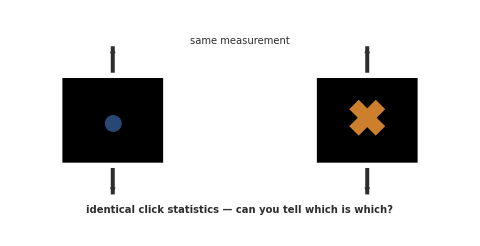

```mathematica
Module[{bx, navy = RGBColor[0.16, 0.28, 0.46], amber = RGBColor[0.8, 0.5, 0.18], ink = GrayLevel[0.18]}, bx = Function[{x, lbl, guts}, {Rectangle[{x - 0.95, -0.8}, {x + 0.95, 0.8}], guts, Black, Text[Style[lbl, 9, Bold], {x, 0.6}]}]; Graphics[{bx[-2.4, "quantum interior", {navy, Disk[{-2.4, -0.05}, 0.16]}], bx[2.4, "classical interior", {amber, Thickness[0.02], Line[{{2.15, -0.2}, {2.65, 0.3}}], Line[{{2.15, 0.3}, {2.65, -0.2}}]}], ink, Thickness[0.006], Arrowheads[0.03], Arrow[{{-2.4, 0.9}, {-2.4, 1.4}}], Arrow[{{2.4, 0.9}, {2.4, 1.4}}], Text[Style["same measurement", 10], {0, 1.5}], Arrow[{{-2.4, -0.9}, {-2.4, -1.4}}], Arrow[{{2.4, -0.9}, {2.4, -1.4}}], Text[Style["identical click statistics — can you tell which is which?", 10, Bold], {0, -1.7}]}, ImageSize -> 480, PlotRange -> {{-3.7, 3.7}, {-1.95, 1.85}}]]
```

Einstein, Podolsky and Rosen (1935) noticed that quantum mechanics allows two systems, once entangled, to show measurement correlations so strong that predicting one system's outcome seems to require instantaneous knowledge of what happens to the other, however far apart they are. Their proposed resolution was that quantum mechanics must be an incomplete description of a deeper, local, realistic theory — one where every outcome is fixed in advance by some (possibly hidden) variable, and nothing travels faster than light.

The experiment, drawn the way it is actually run — one source, two stations, two settings per station, ±1 outcomes:

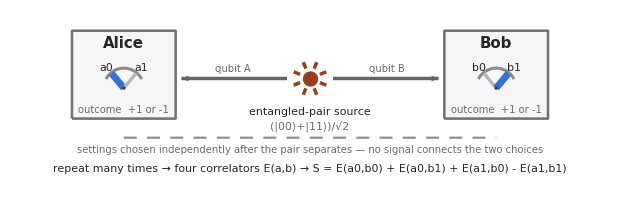

```mathematica
Module[{ink, inkSub, blue, coral, grayL, station, dial}, ink = GrayLevel[0.15]; inkSub = GrayLevel[0.42]; blue = RGBColor[0.2, 0.45, 0.85]; coral = RGBColor[0.6, 0.24, 0.11]; grayL = GrayLevel[0.55]; dial[c_, lbls_, chosen_] := {{grayL, Thickness[0.0035], Circle[c, 0.52, {0.15*Pi, 0.85*Pi}]}, {If[chosen == 1, blue, GrayLevel[0.72]], Thickness[If[chosen == 1, 0.008, 0.004]], Line[{c, c + 0.5*{Cos[0.72*Pi], Sin[0.72*Pi]}}]}, {If[chosen == 2, blue, GrayLevel[0.72]], Thickness[If[chosen == 2, 0.008, 0.004]], Line[{c, c + 0.5*{Cos[0.28*Pi], Sin[0.28*Pi]}}]}, Text[Style[lbls[[1]], 11, ink], c + 0.72*{Cos[0.72*Pi], Sin[0.72*Pi]}], Text[Style[lbls[[2]], 11, ink], c + 0.72*{Cos[0.28*Pi], Sin[0.28*Pi]}], {GrayLevel[0.25], Disk[c, 0.045]}}; station[c_, name_, lbls_, chosen_] := {{EdgeForm[{GrayLevel[0.45], Thickness[0.003]}], FaceForm[GrayLevel[0.965]], Rectangle[c + {-1.35, -1.05}, c + {1.35, 1.25}, RoundingRadius -> 0.15]}, Text[Style[name, 15, Bold, ink], c + {0, 0.95}], dial[c + {0, -0.25}, lbls, chosen], Text[Style["outcome  +1 or -1", 10, inkSub], c + {0, -0.8}]}; Graphics[{{coral, Disk[{0, 0}, 0.2]}, {coral, Thickness[0.004], Table[Line[{0.28*{Cos[a], Sin[a]}, 0.46*{Cos[a], Sin[a]}}], {a, Pi/8, 2*Pi, Pi/4}]}, Text[Style["entangled-pair source", 11, ink], {0, -0.85}], Text[Style["(|00⟩+|11⟩)/√2", 11, inkSub], {0, -1.22}], {GrayLevel[0.4], Thickness[0.004], Arrowheads[0.02], Arrow[{{-0.6, 0}, {-3.35, 0}}], Arrow[{{0.6, 0}, {3.35, 0}}]}, Text[Style["qubit A", 10, inkSub], {-2, 0.28}], Text[Style["qubit B", 10, inkSub], {2, 0.28}], station[{-4.85, 0}, "Alice", {"a0", "a1"}, 1], station[{4.85, 0}, "Bob", {"b0", "b1"}, 2], {GrayLevel[0.55], Dashing[{0.015, 0.012}], Thickness[0.0025], Line[{{-4.85, -1.55}, {4.85, -1.55}}]}, Text[Style["settings chosen independently after the pair separates — no signal connects the two choices", 10, inkSub], {0, -1.85}], Text[Style["repeat many times → four correlators E(a,b) → S = E(a0,b0) + E(a0,b1) + E(a1,b0) - E(a1,b1)", 11, ink], {0, -2.35}]}, PlotRange -> {{-6.6, 6.6}, {-2.7, 1.6}}, ImageSize -> 620, Background -> White]]
```

Bell (1964) showed this is a genuinely testable claim, not just a philosophical preference: any theory where outcomes are fixed by shared hidden variables, with no signal exchanged between the parties, must obey a specific inequality. The version tested in practice is due to Clauser, Horne, Shimony and Holt (1969): two separated parties, Alice and Bob, each choose one of two measurement settings and record a ±1 outcome; forming the combination S = E(a0,b0) + E(a0,b1) + E(a1,b0) − E(a1,b1) of the four correlators, every local hidden-variable theory obeys |S| ≤ 2. Quantum mechanics, given an entangled pair and the right measurement settings, reaches S = 2√2 ≈ 2.828 — Tsirelson's bound (Tsirelson, 1980), strictly above 2.

Build the state that makes this possible, as an actual circuit, using the Wolfram Quantum Computation Framework (loaded once per session; it auto-installs from the public paclet repository the first time — this essay is built against version 2.0.2, which includes two fixes contributed from this project's own bug reports, exercised below):

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

A Hadamard, then a controlled-NOT, applied to two qubits starting at |00⟩ — the standard Bell-pair preparation, drawn natively:

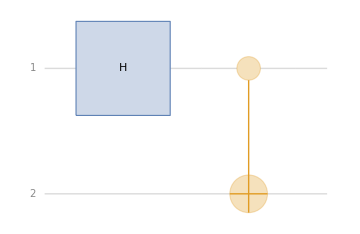

```mathematica
QuantumCircuitOperator[{"H", "CNOT"}]["Diagram"]
```

Apply it, and check genuine entanglement directly — not just correlation, but a state that provably cannot be written as one qubit times another:

```mathematica
QuantumEntangledQ[QuantumCircuitOperator[{"H", "CNOT"}][QuantumState[{1, 0, 0, 0}]]]
```

True

Now read off the four correlators at the settings that saturate CHSH — Pauli Z and X for Alice, their ±45° rotations for Bob — first by direct linear algebra (Pauli matrices, one KroneckerProduct inner product per correlator), the ground truth every later route is checked against:

```mathematica
Module[{sz, sx, bell, a0, a1, b0, b1, corr}, sz = {{1, 0}, {0, -1}}; sx = {{0, 1}, {1, 0}}; bell = {1, 0, 0, 1}/Sqrt[2]; a0 = sz; a1 = sx; b0 = (sz + sx)/Sqrt[2]; b1 = (sz - sx)/Sqrt[2]; corr[a_, b_] := bell . KroneckerProduct[a, b] . bell; FullSimplify[{corr[a0, b0], corr[a0, b1], corr[a1, b0], corr[a1, b1]}]]
```

{1/(√2),1/(√2),1/(√2),-1/(√2)}

```mathematica
corrs = chshCorrelators[]; corrs[[1]] + corrs[[2]] + corrs[[3]] - corrs[[4]]
```

2 √2

The same four correlators can now be computed end-to-end inside the framework itself — each setting pair composed into a joint observable with QuantumTensorProduct, wrapped in QuantumMeasurementOperator, and applied to the circuit-prepared Bell state. That sentence used to be false: when this essay was first assembled, exactly this construction failed with a hard dimension error on every input — one of three reproducible issues in the framework's measurement layer found while building this project, documented and reported upstream, and fixed in version 2.0.2. The EPR experiment now runs as an actual quantum-computation pipeline — state preparation circuit, composite observable, measurement — and returns the same closed forms as the hand computation, checked symbol-for-symbol in the last entry:

Run the EPR/CHSH experiment natively — QuantumTensorProduct for the joint settings, QuantumMeasurementOperator for the statistics — and compare with the direct route:

```mathematica
Module[{bell, sz, sx, a0, a1, b0, b1, corrOf, corrs}, bell = QuantumCircuitOperator[{"H", "CNOT"}][QuantumState[{1, 0, 0, 0}]]; sz = {{1, 0}, {0, -1}}; sx = {{0, 1}, {1, 0}}; a0 = sz; a1 = sx; b0 = (sz + sx)/Sqrt[2]; b1 = (sz - sx)/Sqrt[2]; corrOf[a_, b_] := QuantumMeasurementOperator[QuantumTensorProduct[QuantumOperator[a, {2}, {1}], QuantumOperator[b, {2}, {2}]]][bell]["Mean"]; corrs = FullSimplify[{corrOf[a0, b0], corrOf[a0, b1], corrOf[a1, b0], corrOf[a1, b1]}]; {corrs, FullSimplify[corrs[[1]] + corrs[[2]] + corrs[[3]] - corrs[[4]]], corrs === chshCorrelators[]}]
```

{{1/(√2),1/(√2),1/(√2),-1/(√2)},2 √2,True}

The measurement statistics themselves, not just their sum, are the real content: three settings agree with probability cos^2(π/8) ≈ 0.854 each (correlator +1/√2), the fourth disagrees just as strongly (correlator -1/√2) — and it is exactly this one sign flip, on top of three equal positive correlations, that pushes the sum past the classical ceiling of 2:

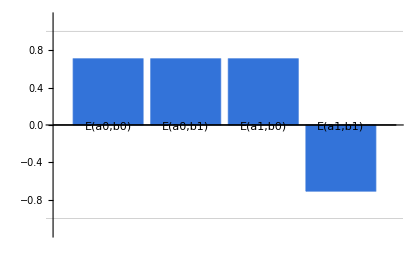

```mathematica
BarChart[N[chshCorrelators[]], ChartLabels -> {"E(a0,b0)", "E(a0,b1)", "E(a1,b0)", "E(a1,b1)"}, ChartStyle -> RGBColor[0.2, 0.45, 0.85], GridLines -> {None, {-1, 1}}, GridLinesStyle -> GrayLevel[0.75], PlotRange -> {-1.15, 1.15}, ImageSize -> 420]
```

Recast as a game: a referee sends independent random bits x to Alice and y to Bob; each answers a bit without communicating; they win if their answers a, b satisfy a⊕b = x∧y, the AND of the questions. Every classical strategy — deterministic or using shared randomness — wins at most 3/4 of the time. Sharing an entangled pair instead lets Alice and Bob win with probability cos^2(π/8) = (2+√2)/4 ≈ 0.854 — a real, provable, experimentally confirmed edge with no classical explanation:

Classical bound, quantum value, and the gap between them:

```mathematica
{3/4, FullSimplify[Cos[Pi/8]^2], N[Cos[Pi/8]^2 - 3/4, 4]}
```

{3/4,Cos[π/8]^2,0.1036}

The resource behind both numbers is entanglement: Alice and Bob share a single quantum state, like the Bell pair (|00⟩+|11⟩)/√2 used above, that cannot be split into “system A in some state” and “system B in some state” separately. Measuring one half instantaneously fixes the statistics of measuring the other, in a way no classical joint distribution over predetermined outcomes can reproduce — yet without letting either party send the other an actual signal: no measurement Alice performs changes Bob's own local statistics, so nothing here permits faster-than-light communication.

CHSH needs two things at once: entanglement, and spatial separation — the two parties must be far enough apart that “no signaling” has real physical teeth. A natural question follows: is separation actually essential, or is entanglement doing all the work alone? Kochen and Specker (1967), and later Klyachko, Can, Binicioglu and Shumovsky (2008), showed the answer is no. A SINGLE quantum system — no entanglement, no separated parties, nothing but one qutrit and a sequence of measurements made on it — already forces the same kind of conclusion: no assignment of pre-existing values to measurement outcomes can reproduce quantum predictions, PROVIDED those values are required not to depend on which OTHER, compatible measurement happens to accompany them. This weaker, more general requirement — that an outcome shouldn't depend on its context, the other compatible measurements grouped with it — is called noncontextuality; its failure, contextuality, is strictly more general than nonlocality, of which Bell/CHSH is only the special spatially-separated case. The KCBS pentagon below is the smallest, sharpest example.

## The Atom: The KCBS Pentagon

The five-cycle exclusivity graph C5 — five measurement outcomes, each excluding its two neighbors — is the smallest object carrying the full classical / quantum / post-quantum hierarchy identified by Cabello, Severini and Winter: the independence number α(C5) = 2 bounds any noncontextual hidden-variable model, the Lovász number ϑ(C5) = √5 — Lovász's own 1979 pentagon example, the result that introduced this graph invariant in the first place — bounds quantum mechanics, and the fractional packing number α*(C5) = 5/2 bounds any no-signalling (post-quantum) theory. Because 2 < √5 < 5/2 strictly, this one pentagon already separates all three levels. Everything below is built by composing copies of this atom.

Build the C5 exclusivity graph:

```mathematica
Graph[CycleGraph[5], VertexStyle -> RGBColor[0.2, 0.45, 0.85], VertexSize -> 0.4, EdgeStyle -> Directive[GrayLevel[0.45], Thickness[0.01]], VertexLabels -> None, GraphLayout -> "CircularEmbedding", ImageSize -> 240, PlotLabel -> "KCBS pentagon: the C5 exclusivity graph"]
```

-Graphics-

The three numbers are three readings of the same five events. Classical: assign each event a definite 0 or 1 in advance; exclusivity forbids two adjacent 1s, so at most two events fire — α(C5) = 2. Quantum: assign each event the probability cos^2 of an actual measurement direction against an actual state; the pentagon geometry below lets every event carry 1/√5 ≈ 0.447 simultaneously — summing to ϑ(C5) = √5. Exclusivity-only: forget mechanics entirely and demand only that adjacent events never both fire; probability 1/2 everywhere is then legal — α*(C5) = 5/2. One pentagon, three ceilings:

Read the same pentagon three ways — best classical assignment, quantum weights, bare-exclusivity halves:

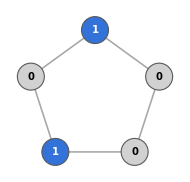
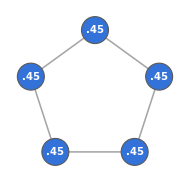
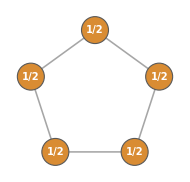

```mathematica
Module[{pts, pent, blue, amber}, blue = RGBColor[0.2, 0.45, 0.85]; amber = RGBColor[0.85, 0.55, 0.2]; pts = Table[{Cos[Pi/2 + 2*Pi*(q/5)], Sin[Pi/2 + 2*Pi*(q/5)]}, {q, 0, 4}]; pent = Function[{vals, cols, sVal, title, sub}, Labeled[Graphics[{{GrayLevel[0.65], Thickness[0.006], Line[Append[pts, First[pts]]]}, Table[{cols[[q]], EdgeForm[GrayLevel[0.35]], Disk[pts[[q]], 0.2], If[MatchQ[cols[[q]], GrayLevel[_]], Black, White], Text[Style[vals[[q]], 10, Bold], pts[[q]]]}, {q, 1, 5}]}, ImageSize -> 190, PlotRange -> 1.45, PlotRangePadding -> 0.12], Column[{Style[title, Bold, 10], Style[sub, Italic, 8, GrayLevel[0.45]], Style[StringJoin["Σp = ", sVal], 13, Bold]}, Alignment -> Center, Spacings -> 0.25], Top]]; Row[{pent[{"1", "0", "1", "0", "0"}, {blue, GrayLevel[0.82], blue, GrayLevel[0.82], GrayLevel[0.82]}, "2", "CLASSICAL", "best 0/1 assignment: α(C5)"], pent[{".45", ".45", ".45", ".45", ".45"}, ConstantArray[blue, 5], "√5 ≃ 2.236", "QUANTUM", "cos^2 weights: ϑ(C5)"], pent[{"1/2", "1/2", "1/2", "1/2", "1/2"}, ConstantArray[amber, 5], "5/2", "EXCLUSIVITY ONLY", "no-signalling ceiling: α*(C5)"]}, Spacer[8]]]
```

KCBS takes its name from Klyachko, Can, Binicioglu and Shumovsky (2008), who derived what they called the “pentagram inequality” for a three-dimensional quantum system (a qutrit): five unit vectors on a cone, each orthogonal to its two cyclic neighbors, giving five dichotomic observables A_i = 1 - 2|v_i⟩⟨v_i| with eigenvalues ±1. Because neighboring directions are orthogonal, the pair (A_i, A_i+1) is jointly measurable — exactly the five edges of the C5 exclusivity graph above. Any noncontextual hidden-variable assignment obeys the cyclic sum Σ ⟨A_i A_i+1⟩ ≥ -3; the qutrit instead reaches Σ = 5 - 4√5 ≈ -3.944 at the cone-axis state, where each projector has quantum probability 1/√5.

Verify the cone-angle geometry live: the per-event quantum probability, and that summing it over all five pentagon events reproduces ϑ(C5):

```mathematica
Simplify[{Cos[Pi/5]/(1 + Cos[Pi/5]), 5*Cos[Pi/5]/(1 + Cos[Pi/5])}]
```

{1/(√5),√5}

The geometry deserves to be seen, and its numbers deserve operational meaning. Each direction v_k is a detector; on the handle state (the cone's axis) it clicks with probability |⟨handle|v_k⟩|^2, and since all five rays lean on the axis at the same angle, all five click probabilities are equal — the blue curve. Exclusivity is the second, sharper requirement: adjacent directions must be perpendicular, so that their projectors commute and can be tested in a single run — and if v_k has just fired, the probability that its neighbor v_(k+1) also fires is the squared overlap |⟨v_k|v_(k+1)⟩|^2, which must be EXACTLY zero for the two events to be mutually exclusive. That crosstalk between supposedly-exclusive detectors is the coral curve, and it is the quantity that makes the cone angle rigid: the two curves meet the KCBS specification at exactly one half-angle, θ* = ArcCos[5^(-1/4)] ≈ 48.06°, where each detector clicks with probability 1/√5 ≈ 0.447 and the crosstalk is exactly zero. Five degrees of detuning already lets “exclusive” detectors co-fire 2.5% of the time. Connecting consecutive tips traces the pentagram that gave KCBS's inequality its original name; every marked value below is measured through QuantumMeasurementOperator, not read off the drawing:

Draw the five directions on their cone, and track both operational probabilities — per-event click rate on the handle state, and neighbor crosstalk after a click — across all cone angles, marking the QuantumMeasurementOperator-computed values at and near θ*:

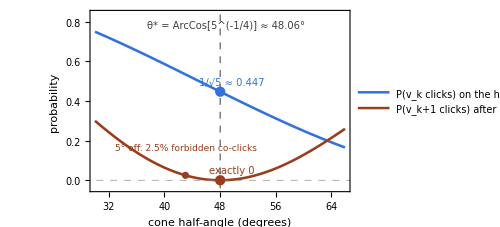
-Graphics3D--Graphics-

```mathematica
Module[{c2, th, vv, vecs, projsAt, handle, qClick, qCross, qCrossOff, tstar, blue, coral, tealc, ink, scene, curves}, blue = RGBColor[0.2, 0.45, 0.85]; coral = RGBColor[0.6, 0.24, 0.11]; tealc = RGBColor[0.06, 0.43, 0.34]; ink = GrayLevel[0.15]; c2 = Cos[Pi/5]/(1 + Cos[Pi/5]); th = ArcCos[Sqrt[c2]]; tstar = N[th/Degree]; vv[t_] := Table[N[{Sin[t]*Cos[4*Pi*(j/5)], Sin[t]*Sin[4*Pi*(j/5)], Cos[t]}, 20], {j, 0, 4}]; vecs = vv[th]; projsAt[t_] := (Outer[Times, #1, #1] & ) /@ vv[t]; handle = QuantumState[{0, 0, 1}, 3]; qClick = QuantumMeasurementOperator[projsAt[th][[1]]][handle]["Mean"]; qCross = QuantumMeasurementOperator[projsAt[th][[2]]][QuantumState[vecs[[1]], 3]]["Mean"]; qCrossOff = QuantumMeasurementOperator[projsAt[th - 5*Degree][[2]]][QuantumState[vv[th - 5*Degree][[1]], 3]]["Mean"]; scene = Graphics3D[{{Opacity[0.12], tealc, Cone[{{0, 0, 1.02}, {0, 0, 0}}, 1.02*Tan[th]]}, {coral, Thickness[0.006], Arrowheads[0.03], Arrow[{{0, 0, 0}, {0, 0, 1.24}}]}, Text[Style["axis = handle state", 10, coral], {0, 0, 1.56}], Table[{blue, Thickness[0.005], Arrowheads[0.025], Arrow[{{0, 0, 0}, N[vecs[[j]]]}], Text[Style[Subscript["v", j - 1], 12, ink], 1.19*N[vecs[[j]]]]}, {j, 5}], {Darker[tealc, 0.1], Thickness[0.004], Table[Line[{N[vecs[[j]]], N[vecs[[Mod[j, 5] + 1]]]}], {j, 5}]}}, Boxed -> False, ImageSize -> 300, PlotRange -> {{-1.35, 1.35}, {-1.35, 1.35}, {-0.05, 1.68}}, ViewPoint -> {2.6, -2.2, 1.4}]; curves = Plot[{Cos[t*Degree]^2, (Cos[t*Degree]^2 + Sin[t*Degree]^2*Cos[4*(Pi/5)])^2}, {t, 30, 66}, PlotStyle -> {{blue, Thickness[0.005]}, {coral, Thickness[0.005]}}, PlotLegends -> Placed[{"P(v_k clicks) on the handle state", "P(v_k+1 clicks) after v_k fired — crosstalk"}, Below], FrameLabel -> {"cone half-angle (degrees)", "probability"}, Frame -> True, PlotRange -> {{30, 66}, {-0.04, 0.84}}, GridLines -> {None, {0}}, GridLinesStyle -> Directive[GrayLevel[0.55], Dashed], LabelStyle -> Directive[10, GrayLevel[0.3]], ImageSize -> 370, Epilog -> {{GrayLevel[0.45], Dashed, Line[{{tstar, -0.04}, {tstar, 0.84}}]}, Text[Style["θ* = ArcCos[5^(-1/4)] ≈ 48.06°", 10, GrayLevel[0.25]], {tstar + 0.8, 0.79}, {-1, 0}], {blue, PointSize[0.02], Point[{tstar, N[qClick]}]}, Text[Style["1/√5 ≈ 0.447", 10, blue], {tstar + 1.6, N[qClick] + 0.05}, {-1, 0}], {coral, PointSize[0.02], Point[{tstar, N[qCross]}]}, Text[Style["exactly 0", 10, coral], {tstar + 1.6, N[qCross] + 0.05}, {-1, 0}], {coral, PointSize[0.014], Point[{tstar - 5, N[qCrossOff]}]}, Text[Style["5° off: 2.5% forbidden co-clicks", 9, coral], {tstar - 5, N[qCrossOff] + 0.14}, {0.25, 0}]}]; Row[{scene, curves}, Spacer[10]]]
```

The same facts, exactly rather than visually — all five adjacent dot products vanish identically, the directions are unit vectors, and the pentagon's three ceilings are the closed forms promised above:

```mathematica
Module[{c2, vecs}, c2 = Cos[Pi/5]/(1 + Cos[Pi/5]); vecs = Table[{Sqrt[1 - c2] Cos[4 Pi i/5], Sqrt[1 - c2] Sin[4 Pi i/5], Sqrt[c2]}, {i, 0, 4}]; {Table[Simplify[vecs[[i]].vecs[[Mod[i, 5] + 1]]], {i, 5}], Simplify[vecs[[1]].vecs[[1]]], {2, Sqrt[5], 5/2}}]
```

{{0,0,0,0,0},1,{2,√5,5/2}}

Why five, and not fewer? Each observable is dichotomic, and orthogonal neighbors force joint measurability, so a cycle of any length is available to test. But even cycles saturate the classical bound quantum-mechanically (no advantage), and the smallest odd cycle, C3, already collapses: three mutually orthogonal directions in a 3-dimensional Hilbert space form a single shared context rather than three separate ones (pairwise-compatible sharp measurements are here jointly compatible), so no contextuality can appear. C5 is the smallest cycle where this collapse does not happen — the genuine atom of contextuality.

Classical, quantum and ceiling values for the three smallest odd cycles, live — C3 collapses to a single value; C5 and C7 do not:

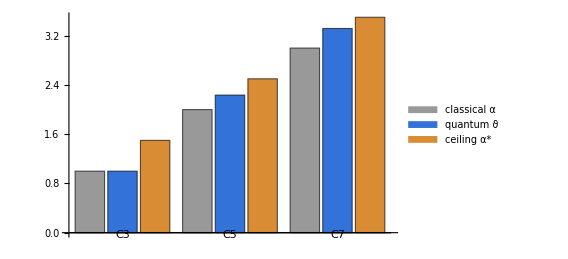

```mathematica
BarChart[{{1, N[thetaOddCycle[3]], 3/2}, {2, N[thetaOddCycle[5]], 5/2}, {3, N[thetaOddCycle[7]], 7/2}}, ChartLabels -> {{"C3", "C5", "C7"}, None}, ChartLegends -> {"classical α", "quantum ϑ", "ceiling α*"}, ChartStyle -> {GrayLevel[0.6], RGBColor[0.2, 0.45, 0.85], RGBColor[0.85, 0.55, 0.2]}, ImageSize -> 420]
```

Everything so far used geometry and graph invariants. Now run the pentagon as an actual measurement, through the framework's own measurement object: each projector |v_k⟩⟨v_k| becomes a QuantumMeasurementOperator, applied to the handle state. This computation is also a regression test with a history: in framework version 2.0.1 these exact five calls silently returned a wrong probability for two of the five structurally-identical projectors — no message, no warning, just a different number — one of three reproducible issues found while building this project, documented in its bug report and fixed upstream in version 2.0.2. The pentagon's five-fold symmetry makes the correct answer unmistakable: all five probabilities must be equal, and their sum must be ϑ(C5):

Measure each KCBS projector on the handle state through QuantumMeasurementOperator — five equal probabilities 1/√5, summing to √5:

```mathematica
Module[{c2, vecs, projs, handle, means}, c2 = Cos[Pi/5]/(1 + Cos[Pi/5]); vecs = N[Table[{Sqrt[1 - c2]*Cos[4*Pi*(i/5)], Sqrt[1 - c2]*Sin[4*Pi*(i/5)], Sqrt[c2]}, {i, 0, 4}], 20]; projs = (Outer[Times, #1, #1] & ) /@ vecs; handle = QuantumState[{0, 0, 1}, 3]; means = Table[QuantumMeasurementOperator[p][handle]["Mean"], {p, projs}]; {means, Total[means], N[Sqrt[5], 20]}]
```

{{0.4472135954999579,0.44721359549996,0.447213595499958,0.447213595499958,0.44721359549996},2.23606797749979,2.2360679774997896964}

The full KCBS inequality now follows from the same pipeline. Each event becomes a dichotomic observable A_k = 1 - 2|v_k⟩⟨v_k|; adjacent pairs commute (their directions are orthogonal), so each product A_k A_(k+1) is itself a single jointly-measurable observable — one measurement context per pentagon edge. Any noncontextual assignment of pre-existing ±1 values obeys Σ ≥ -3; the qutrit's five contexts each return ⟨A_k A_(k+1)⟩ = 1 - 4/√5 ≈ -0.789, summing to 5 - 4√5 ≈ -3.944. This negative correlation form is the one experiments report — but it is the essay's positive event form in disguise: adjacent projector products vanish identically, so Σ⟨A_k A_(k+1)⟩ = 5 - 4·Σp EXACTLY, an affine change of ruler and nothing more. The last entry below converts the measured correlation sum back onto the event ruler and lands on √5 — the same number the five projector probabilities summed to above:

Measure the five contexts — the commuting products A_k A_(k+1) — through QuantumMeasurementOperator, sum them against the noncontextual bound -3, and convert back to the event ruler:

```mathematica
Module[{c2, vecs, projs, obs, handle, prod, corr}, c2 = Cos[Pi/5]/(1 + Cos[Pi/5]); vecs = N[Table[{Sqrt[1 - c2]*Cos[4*Pi*(i/5)], Sqrt[1 - c2]*Sin[4*Pi*(i/5)], Sqrt[c2]}, {i, 0, 4}], 20]; projs = (Outer[Times, #1, #1] & ) /@ vecs; obs = (IdentityMatrix[3] - 2*#1 & ) /@ projs; handle = QuantumState[{0, 0, 1}, 3]; prod[k_] := Module[{m = obs[[k]] . obs[[Mod[k, 5] + 1]]}, (m + ConjugateTranspose[m])/2]; corr = Table[QuantumMeasurementOperator[prod[k]][handle]["Mean"], {k, 5}]; {corr, Total[corr], N[5 - 4*Sqrt[5], 20], -3, (5 - Total[corr])/4}]
```

{{-0.78885438199983,-0.78885438199983,-0.788854381999832,-0.78885438199983,-0.78885438199983},-3.9442719099992,-3.9442719099991587856,-3,2.23606797749979}

Now place every landmark on one line, in the essay's own convention — the event sum Σp — with nothing quoted: the classical wall α(C5) = 2 is computed by FindIndependentVertexSet, the exclusivity-only ceiling α*(C5) = 5/2 by an exact linear program over the fractional-packing polytope, the qutrit marker is the QuantumMeasurementOperator probability sum itself, and the Lapkiewicz measurement is converted from its reported form, -3.893(6) → Σp = 2.2233(15). The reported correlation ruler runs beneath, tied to this one by Σ⟨A_k A_(k+1)⟩ = 5 - 4Σp:

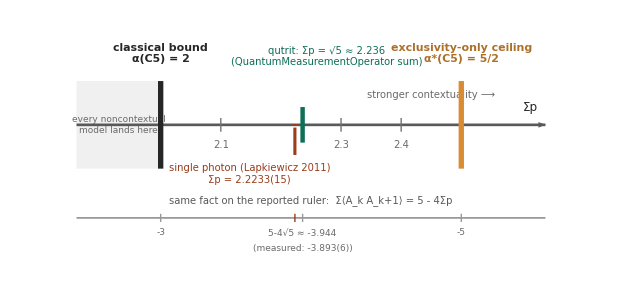

```mathematica
Module[{ink, inkSub, coral, tealc, amber, alphaC, alphaStar, thetaQ, measuredP, c2, vecs, projs, handle, vars, tick}, ink = GrayLevel[0.15]; inkSub = GrayLevel[0.42]; coral = RGBColor[0.6, 0.24, 0.11]; tealc = RGBColor[0.06, 0.43, 0.34]; amber = RGBColor[0.85, 0.55, 0.2]; alphaC = Length[First[FindIndependentVertexSet[CycleGraph[5]]]]; vars = Array[x, 5]; alphaStar = MaxValue[{Total[vars], And @@ Table[x[i] + x[Mod[i, 5] + 1] <= 1, {i, 5}] && And @@ Table[x[i] >= 0, {i, 5}]}, vars]; c2 = Cos[Pi/5]/(1 + Cos[Pi/5]); vecs = N[Table[{Sqrt[1 - c2]*Cos[4*Pi*(i/5)], Sqrt[1 - c2]*Sin[4*Pi*(i/5)], Sqrt[c2]}, {i, 0, 4}], 20]; projs = (Outer[Times, #1, #1] & ) /@ vecs; handle = QuantumState[{0, 0, 1}, 3]; thetaQ = N[Total[Table[QuantumMeasurementOperator[p][handle]["Mean"], {p, projs}]]]; measuredP = (5 - -3.893)/4; tick[x0_, lbl_] := {{GrayLevel[0.45], Line[{{x0, -0.05}, {x0, 0.05}}]}, Text[Style[lbl, 10, inkSub], {x0, -0.15}]}; Graphics[{{FaceForm[GrayLevel[0.94]], Rectangle[{1.86, -0.32}, {alphaC, 0.32}]}, Text[Style["every noncontextual\nmodel lands here", 9, inkSub], {1.93, 0.}], {GrayLevel[0.35], Thickness[0.003], Arrowheads[{{0.02, 1}}], Arrow[{{1.86, 0}, {2.64, 0}}]}, tick[2.1, "2.1"], tick[2.3, "2.3"], tick[2.4, "2.4"], Text[Style["stronger contextuality ⟶", 10, inkSub], {2.45, 0.22}], Text[Style["Σp", 12, ink], {2.615, 0.13}], {ink, Thickness[0.006], Line[{{alphaC, -0.32}, {alphaC, 0.32}}]}, Text[Style["classical bound\nα(C5) = 2", 11, Bold, ink], {alphaC, 0.52}], {amber, Thickness[0.006], Line[{{N[alphaStar], -0.32}, {N[alphaStar], 0.32}}]}, Text[Style["exclusivity-only ceiling\nα*(C5) = 5/2", 11, Bold, Darker[amber, 0.2]], {N[alphaStar], 0.52}], {tealc, Thickness[0.005], Line[{{thetaQ, -0.13}, {thetaQ, 0.13}}]}, {tealc, Disk[{thetaQ, 0}, 0.006]}, Text[Style["qutrit: Σp = √5 ≈ 2.236\n(QuantumMeasurementOperator sum)", 10, tealc], {thetaQ + 0.04, 0.5}], {coral, Disk[{measuredP, 0}, 0.006]}, {coral, Thickness[0.0035], Line[{{measuredP, -0.22}, {measuredP, -0.02}}]}, Text[Style["single photon (Lapkiewicz 2011)\nΣp = 2.2233(15)", 10, coral], {measuredP - 0.075, -0.36}], Text[Style["same fact on the reported ruler:  Σ⟨A_k A_k+1⟩ = 5 - 4Σp", 10, GrayLevel[0.35]], {2.25, -0.55}], {GrayLevel[0.6], Thickness[0.002], Line[{{1.86, -0.68}, {2.64, -0.68}}]}, {GrayLevel[0.6], Line[{{alphaC, -0.71}, {alphaC, -0.65}}], Line[{{thetaQ, -0.71}, {thetaQ, -0.65}}], Line[{{N[alphaStar], -0.71}, {N[alphaStar], -0.65}}]}, {coral, Line[{{measuredP, -0.71}, {measuredP, -0.65}}]}, Text[Style["-3", 9, inkSub], {alphaC, -0.79}], Text[Style["5-4√5 ≈ -3.944", 9, inkSub], {thetaQ, -0.79}], Text[Style["-5", 9, inkSub], {N[alphaStar], -0.79}], Text[Style["(measured: -3.893(6))", 9, inkSub], {thetaQ, -0.9}]}, PlotRange -> {{1.83, 2.7}, {-1., 0.72}}, AspectRatio -> 0.45, ImageSize -> 640, Background -> White]]
```

This is not only a mathematical construction. Lapkiewicz et al. (2011) realized it with a single heralded photon carrying three optical modes — an actual qutrit — reconfiguring one physical apparatus into five different wave-plate settings so that the detector shared between neighboring contexts is never touched between measurements, enforcing compatibility by construction rather than by assumption. The measured correlation sum was Σ = -3.893(6), violating the classical bound by more than 120 standard deviations.

The apparatus, schematically — three optical paths of one heralded photon are the qutrit; the five KCBS directions are five settings of the same interferometer, so the shared detector between neighboring contexts is physically the same detector:

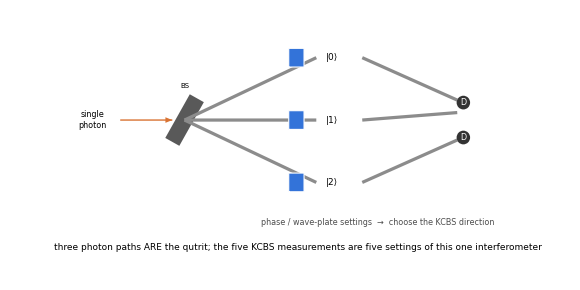

```mathematica
Graphics[{{RGBColor[0.85, 0.45, 0.2], Arrowheads[0.025], Arrow[{{-2.6, 0}, {-1.75, 0}}]}, Black, Text[Style["single\nphoton", 8], {-3.05, 0}], {GrayLevel[0.35], Thickness[0.02], Line[{{-1.75, -0.35}, {-1.35, 0.35}}]}, Text[Style["BS", 7], {-1.55, 0.55}], {GrayLevel[0.55], Thickness[0.004], Line[{{-1.55, 0}, {0.6, 1.}}], Line[{{-1.55, 0}, {0.6, 0}}], Line[{{-1.55, 0}, {0.6, -1.}}]}, Black, Text[Style["|0⟩", 9], {0.85, 1.}], Text[Style["|1⟩", 9], {0.85, 0}], Text[Style["|2⟩", 9], {0.85, -1.}], {RGBColor[0.2, 0.45, 0.85], EdgeForm[White], Rectangle[{0.15, 0.85}, {0.4, 1.15}], Rectangle[{0.15, -0.15}, {0.4, 0.15}], Rectangle[{0.15, -1.15}, {0.4, -0.85}]}, GrayLevel[0.3], Text[Style["phase / wave-plate settings  →  choose the KCBS direction", 8], {1.6, -1.65}], {GrayLevel[0.55], Thickness[0.004], Line[{{1.35, 1.}, {2.9, 0.32}}], Line[{{1.35, 0}, {2.9, 0.12}}], Line[{{1.35, -1.}, {2.9, -0.32}}]}, {GrayLevel[0.2], Disk[{3., 0.28}, 0.11], Disk[{3., -0.28}, 0.11]}, White, Text[Style["D", 8], {3., 0.28}], Text[Style["D", 8], {3., -0.28}], Black, Text[Style["three photon paths ARE the qutrit; the five KCBS measurements are five settings of this one interferometer", 9], {0.3, -2.05}]}, ImageSize -> 580, PlotRange -> {{-3.7, 3.9}, {-2.3, 1.5}}, ImagePadding -> 6]
```

That reconfiguration — one setting to the next, never a fresh re-derivation — is a genuine gate cascade on the same qutrit, built here through the Wolfram Quantum Computation Framework rather than asserted: five measurement-context frames, each an orthonormal basis built from two adjacent (hence jointly measurable) KCBS directions plus their cross product, linked by four incremental transition rotations:

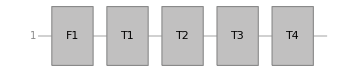

```mathematica
QuantumCircuitOperator[lapkiewiczGates[]]["Diagram"]
```

One wire, five gates: F1 rotates the input into context 1's own measurement basis; each T_k then advances by exactly one incremental reconfiguration step. Applying the growing gate chain (F1; F1,T1; ...; F1,T1,T2,T3,T4) to the pentagon's own symmetry axis and reading the resulting amplitude off the circuit's own matrix gives every context's click probability directly — the route originally chosen when QuantumMeasurementOperator still carried the two bugs found here (since fixed in 2.0.2 and exercised on these same projectors above), kept because it makes the two independent pipelines confirm each other:

```mathematica
Module[{gates, circuits, handle, probs}, gates = lapkiewiczGates[]; circuits = Table[QuantumCircuitOperator[Take[gates, k + 1]], {k, 0, 4}]; handle = {0., 0., 1.}; probs = Table[Abs[(circuits[[k + 1]]["Matrix"] . handle)[[1]]]^2, {k, 0, 4}]; {AllTrue[circuits, #1["UnitaryQ"] & ], probs, Total[probs], N[Sqrt[5]]}]
```

{True,{0.447214,0.447214,0.447214,0.447214,0.447214},2.23607,2.23607}

All five circuits are unitary, and all five give the same probability, 1/√5, exactly — the pentagon's own five-fold symmetry guarantees every context is equivalent, and the gate cascade respects that exactly rather than approximately, summing to ϑ(C5) = √5 across all five settings.

The same bound ϑ(C5) = √5 has a second derivation that anticipates the rest of this essay: take two independent copies of the pentagon. Their 25 joint events form the exclusivity graph built from the co-normal (OR) product of the two C5's — the same composition operation named again in the next section, but applied here to independent copies rather than glued neighbors. Quantum mechanics saturates it at ϑ = 5 exactly, and Lovász-number multiplicativity under the OR product forces the single-copy value back down to ϑ(C5) = √5. The two ways of combining pentagons this essay is built around — independent copies and edge-gluing — already show up, in miniature, inside the atom's own quantum bound.

That saturation is measurable, and now measured natively: on the doubled handle state, every one of the 25 joint projectors P_i ⊗ P_j clicks with probability exactly (1/√5)^2 = 1/5, and the 25 of them sum to exactly 5. Measuring a composite observable like P_i ⊗ P_j through QuantumMeasurementOperator is precisely the operation that used to fail outright (the tensor-product bug fixed in framework 2.0.2) — the very computation this essay's composition story runs on:

Measure all 25 tensor-product projectors of two independent pentagons on the doubled handle state — one distinct value, 1/5, and the saturating total:

```mathematica
Module[{c2, vecs, projs, handle2, mean, means25}, c2 = Cos[Pi/5]/(1 + Cos[Pi/5]); vecs = N[Table[{Sqrt[1 - c2]*Cos[4*Pi*(i/5)], Sqrt[1 - c2]*Sin[4*Pi*(i/5)], Sqrt[c2]}, {i, 0, 4}], 20]; projs = (Outer[Times, #1, #1] & ) /@ vecs; handle2 = QuantumState[Flatten[KroneckerProduct[{0, 0, 1}, {0, 0, 1}]], {3, 3}]; mean[i_, j_] := QuantumMeasurementOperator[QuantumTensorProduct[QuantumOperator[projs[[i]], {3}, {1}], QuantumOperator[projs[[j]], {3}, {2}]]][handle2]["Mean"]; means25 = Flatten[Table[mean[i, j], {i, 5}, {j, 5}]]; {DeleteDuplicates[Round[means25, 10^(-10)]], Total[means25]}]
```

{{1/5},5.}

## Composition by Gluing: Direct and Twisted

There are two distinct ways to compose several pentagons into a larger scenario. One is to take independent copies and combine them with the co-normal (OR) product of their exclusivity graphs — a route this project studies separately. The other, below, is graph surgery: literally sharing a detector between neighboring pentagons, gluing them edge-to-edge into a chain or a ring. At every shared joint there are exactly two ways to attach the next pentagon, called direct and twisted — named for what each does to the pentagon's own cyclic vertex order: direct advances it by a rotation, twisted reverses it by a reflection. Both are genuine elements of the pentagon's symmetry group, built from and verified directly against the KCBS vectors v_k introduced above:

Apply each joint type to the pentagon's own vertex labels: direct rotates 0->1->2->3->4->0 (determinant +1); twisted reflects across the axis through vertex 2, fixing it and swapping 0 with 4, 1 with 3 (determinant -1):

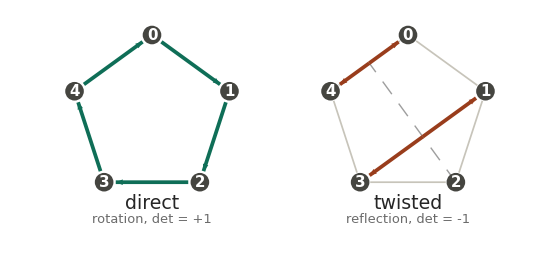

```mathematica
Module[{coral, grayN, grayLine, teal, ink, inkSub, pentAngles, Rp, nodeRp, pentUnit, directC, twistedC, directPos, twistedPos, trimSeg, directArrows, directNodes, directLabels, twistedOutline, axisLine, swapPair, swap04, swap13, twistedNodes, twistedLabels, titles}, coral = RGBColor[0.6, 0.24, 0.11]; grayN = RGBColor[0.27, 0.27, 0.25]; grayLine = RGBColor[0.78, 0.77, 0.73]; teal = RGBColor[0.06, 0.43, 0.34]; ink = GrayLevel[0.15]; inkSub = GrayLevel[0.42]; pentAngles = Table[(90 - 72*k)*Degree, {k, 0, 4}]; Rp = 2.1; nodeRp = 0.24; pentUnit = Table[Rp*{Cos[a], Sin[a]}, {a, pentAngles}]; directC = {-3.3, 0}; twistedC = {3.3, 0}; directPos = (directC + #1 & ) /@ pentUnit; twistedPos = (twistedC + #1 & ) /@ pentUnit; trimSeg[a_, b_, gap_:0.3] := Module[{u = (b - a)/Norm[b - a]}, {a + gap*u, b - gap*u}]; directArrows = Table[{teal, Thickness[0.0048], Arrowheads[0.032], Arrow[trimSeg[directPos[[k + 1]], directPos[[Mod[k + 1, 5] + 1]]]]}, {k, 0, 4}]; directNodes = Table[{grayN, Disk[directPos[[k + 1]], nodeRp]}, {k, 0, 4}]; directLabels = Table[Text[Style[ToString[k], 15, White, Bold], directPos[[k + 1]]], {k, 0, 4}]; twistedOutline = Table[{grayLine, Thickness[0.0022], Line[trimSeg[twistedPos[[k + 1]], twistedPos[[Mod[k + 1, 5] + 1]], 0.26]]}, {k, 0, 4}]; axisLine = {GrayLevel[0.62], Thickness[0.0018], Dashing[{0.02, 0.015}], Line[{twistedPos[[3]], Mean[{twistedPos[[5]], twistedPos[[1]]}]}]}; swapPair[a_, b_] := Module[{mid = Mean[{a, b}], u}, u = (b - a)/Norm[b - a]; {coral, Thickness[0.0048], Arrowheads[0.032], Arrow[{mid, b - 0.3*u}], Arrow[{mid, a + 0.3*u}]}]; swap04 = swapPair[twistedPos[[1]], twistedPos[[5]]]; swap13 = swapPair[twistedPos[[2]], twistedPos[[4]]]; twistedNodes = Table[{grayN, Disk[twistedPos[[k + 1]], nodeRp]}, {k, 0, 4}]; twistedLabels = Table[Text[Style[ToString[k], 15, White, Bold], twistedPos[[k + 1]]], {k, 0, 4}]; titles = {Text[Style["direct", 19, ink], directC + {0, -2.25}], Text[Style["rotation, det = +1", 13, inkSub], directC + {0, -2.65}], Text[Style["twisted", 19, ink], twistedC + {0, -2.25}], Text[Style["reflection, det = -1", 13, inkSub], twistedC + {0, -2.65}]}; Graphics[{directArrows, directNodes, directLabels, twistedOutline, axisLine, swap04, swap13, twistedNodes, twistedLabels, titles}, PlotRange -> {{-5.9, 5.9}, {-3., 2.4}}, ImageSize -> 560, Background -> White]]
```

Both operations act on a genuine physical qutrit — the same three-dimensional system the KCBS pentagon already lives in — so they compose as an actual quantum circuit, not just an abstract permutation of labels. Built and verified natively through the Wolfram Quantum Computation Framework, chaining two direct steps then one twisted step — the (ddt) pattern:

Build R_direct and R_twisted as qutrit gates and assemble the (ddt) circuit:

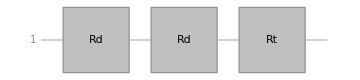

```mathematica
QuantumCircuitOperator[{QuantumOperator[Rdirect, 3, "Label" -> "Rd"], QuantumOperator[Rdirect, 3, "Label" -> "Rd"], QuantumOperator[Rtwisted, 3, "Label" -> "Rt"]}, "Label" -> "ddt step"]["Diagram"]
```

Both single-qutrit gates, and the assembled three-gate circuit, are confirmed unitary by the framework itself — not merely asserted — and the circuit's own matrix has determinant exactly -1: two rotations compose to a rotation, and the one reflection flips the overall parity. This is the same fact, now checked as an actual gate sequence rather than argued combinatorially, that makes a single twisted joint irreducible while two consecutive ones partially cancel — the reason ddt (isolated flips) beats pure twisted (paired flips) later in this essay:

```mathematica
{QuantumOperator[Rdirect, 3]["UnitaryQ"], QuantumOperator[Rtwisted, 3]["UnitaryQ"], Det[QuantumCircuitOperator[{QuantumOperator[Rdirect, 3], QuantumOperator[Rdirect, 3], QuantumOperator[Rtwisted, 3]}]["Matrix"]]}
```

{True,True,-1.}

Why exactly two ways to attach at a joint — not more, not fewer? Because the number of surviving attachments is set by the size of the interface: the part of the next pentagon's frame that the joint pins down. A rigid attachment is an isometry of the same real three-dimensional space the qutrit lives in, and it must match the pin. Pin one shared edge — two orthonormal directions — and the isometry is already determined on the plane they span, so the only freedom left is the sign on the one-dimensional orthogonal complement: exactly two attachments, separated by exactly det = ±1. Direct and twisted are not two choices among many — they are the entire solution set, and R_twisted = diag(1,1,-1).R_direct displays the leftover sign flip literally. Pin only a shared vertex — one direction — and a whole circle of rotations about it survives: a continuum of genuinely different attachments that the determinant no longer separates (every one has det = +1), which is why a vertex-glued mesh admits no two-letter word description. Pin two shared edges — three independent directions — and nothing survives: the map is forced outright, sign included, and the “new” pentagon collapses onto the old one. Edge-gluing is the unique interface size at which composition becomes a discrete binary choice — the reason an infinite gluing strategy is exactly a word in {d,t}, and the reason the de Bruijn machinery of the closing sections applies at all. All three regimes are counted below, exactly:

Pin one edge, one vertex, then two edges of the pentagon frame, and solve for every isometry matching the pin — two attachments (reconstructing R_direct and R_twisted exactly), a continuum (held for a symbolic spin angle phi), and a single forced map, respectively:

```mathematica
Module[{c2, vv, attach, edgePair, spin, phi, samples, Vmat, Wmat, Rforced, Rd, Rt}, c2 = Cos[Pi/5]/(1 + Cos[Pi/5]); vv[k_] := {Sqrt[c2], Sqrt[1 - c2]*Cos[4*Pi*(k/5)], Sqrt[1 - c2]*Sin[4*Pi*(k/5)]}; Rd = RotationMatrix[4*(Pi/5), {1, 0, 0}]; Rt = DiagonalMatrix[{1, 1, -1}] . Rd; attach[{a1_, a2_}, {b1_, b2_}, s_] := Transpose[{b1, b2, s*Cross[b1, b2]}] . {a1, a2, Cross[a1, a2]}; edgePair = {attach[{vv[0], vv[1]}, {vv[1], vv[2]}, 1], attach[{vv[0], vv[1]}, {vv[1], vv[2]}, -1]}; spin[a_] := RotationMatrix[a, vv[0]]; samples = Table[spin[a] . vv[1], {a, 2*(Pi/5), 2*Pi, 2*(Pi/5)}]; Vmat = Transpose[{vv[0], vv[1], vv[2]}]; Wmat = Transpose[{vv[1], vv[2], vv[3]}]; Rforced = Wmat . Inverse[Vmat]; Association["one edge pinned: dets of the two surviving attachments" -> FullSimplify[Det /@ edgePair], "  the det +1 one is R_direct, exactly" -> FullSimplify[edgePair[[1]] == Rd], "  the det -1 one for the mirrored target is R_twisted, exactly" -> FullSimplify[attach[{vv[0], vv[1]}, {vv[4], vv[3]}, -1] == Rt], "one vertex pinned: interface held at every spin angle phi, always det +1" -> FullSimplify[spin[phi] . vv[0] == vv[0] && Det[spin[phi]] == 1], "  distinct attachments among five sample spin angles" -> Length[DeleteDuplicates[Round[N[samples], 10^(-10)]]], "two edges pinned: forced map is orthogonal, is R_direct, sign no longer free" -> FullSimplify[{Rforced . Transpose[Rforced] == IdentityMatrix[3], Rforced == Rd, Det[Rforced]}]]]
```

<|one edge pinned: dets of the two surviving attachments→{1,-1},  the det +1 one is R_direct, exactly→True,  the det -1 one for the mirrored target is R_twisted, exactly→True,one vertex pinned: interface held at every spin angle phi, always det +1→True,  distinct attachments among five sample spin angles→5,two edges pinned: forced map is orthogonal, is R_direct, sign no longer free→{True,True,1}|>

For a ring built entirely from one orientation, both closed forms below are proven theorems, not numerical fits — derived here, not merely cited. Start with the direct ring's ϑ: deleting the N glue edges leaves a disjoint union C_N ⊔ C_2N (the inner rail plus the outer cycle); ϑ never decreases under edge deletion, is additive on disjoint unions, and ϑ(C_2N) = N since even cycles are perfect — giving the upper bound ϑ(direct-ring N) ≤ N + ϑ(C_N). A matching lower bound comes from an explicit vector representation: take an optimal representation of the rail C_N, append one dimension, and assign every outer vertex the same fresh basis vector — every edge then either repeats a rail orthogonality or pairs with the new dimension, so the construction is feasible and attains exactly N + ϑ(C_N).

Spot-check the representation witness at four odd N — cyclic orthogonality (including wrap-around), unit norm, and the value identity all verified live:

```mathematica
Module[{w = Pi*((n - 1)/n), ca2, u, handle}, ca2 = Cos[Pi/n]/(1 + Cos[Pi/n]); u[k_] := {Sqrt[ca2], Sqrt[1 - ca2]*Cos[k*w], Sqrt[1 - ca2]*Sin[k*w], 0}; handle = {1, 0, 0, 0}; AllTrue[Range[0, n - 1], FullSimplify[u[#1] . u[Mod[#1 + 1, n]]] === 0 & ] && AllTrue[Range[0, n - 1], FullSimplify[u[#1] . u[#1]] === 1 & ] && FullSimplify[Sum[(handle . u[k])^2, {k, 0, n - 1}] + n - (n + n*(Cos[Pi/n]/(1 + Cos[Pi/n])))] === 0]
```

{True,True,True,True}

The matching α bound comes from counting, not geometry: every pentagon induces its own C5 (independence number 2), and summing this window bound over all N pentagons counts each glue's shared vertices twice and its free vertex once, giving 2·(shared) + (free) ≤ 2N and hence α ≤ ⌊3N/2⌋; the alternating set of every free vertex plus every other rail vertex attains it. For even N this already forces ϑ = α = α* = 3N/2 exactly — no possible gap, at any level of the hierarchy.

At odd N the gap does not vanish — but it does not grow either. Using ϑ(C_N) = N Cos[π/N]/(1+Cos[π/N]) for odd N together with α = (3N-1)/2, the gap works out to ϑ(C_N) - (N-1)/2; expand it as N → ∞:

```mathematica
Series[n*Cos[Pi/n]/(1 + Cos[Pi/n]) - (n - 1)/2, {n, Infinity, 2}]
```

1/2-π^2/(8 n)+O[1/n]^3

So odd-N direct rings approach a fixed ceiling of 1/2 as N grows, closing in at rate π^2/(8N) — compare the series' N -> 17 prediction against the 0.4270 already plotted in Figure 4 below. Direct is bounded regardless of size; twisted, next, is not.

The twisted ring's ϑ ≈ τ*·N is likewise not a fit: τ* is an exact algebraic closed form. As N → ∞ the ring's ϑ-SDP reduces to a continuum symbol minimax; the ring's reflection symmetry forces one dual variable to equal another (βbx = γax), and the KKT stationarity condition factors as (u-2g)(u+2gc) = 0, forcing a second relation (βab = 2γba). Substituting both into the remaining system and eliminating variables by Gröbner-basis computation collapses it to a single cubic, 49x^3 - 128x^2 - 75x + 218 = 0, and τ* is its middle root, ≈ 1.376718.

Certify τ* as a genuine solution: exhibit the explicit dual witness (g, h, cos θ*) in the cubic field ℚ(τ*) and verify all three KKT/feasibility identities vanish exactly:

```mathematica
Module[{gW, hW, cW}, {gW, hW, cW} = {(53*tauStar^2 - 121*tauStar + 218)/458, (327 - 67*tauStar - 35*tauStar^2)/229, (1715*tauStar^2 + 77*tauStar - 3428)/916}; RootReduce[Flatten[{gW*tauStar - hW^2*(1 + 2*cW), tauStar^2 - (3 - 3*gW)*tauStar + (2 - 3*gW) - 2*(1 - hW)^2, CoefficientList[tauStar^3 - (5*gW^2 + 4*gW^2*c + 2*hW^2)*tauStar + 2*hW^2*gW*(2*c + 2*c^2 - 1) - 4*gW*hW^2*(c - cW)^2, c]}]]]
```

{0,0,0,0}

Global optimality — not just a stationary point — follows because the symbol program is a max-eigenvalue minimax, hence convex, and this witness has both KKT multipliers positive. With both orientations now proven, not asserted: a direct ring of N pentagons has ϑ = N + ϑ(C_N) and α = ⌊3N/2⌋ (gap = 0 at even N, → 1/2 at odd N); a twisted ring has ϑ ≈ τ*·N and α = ⌊4N/3⌋ (gap = (τ*-4/3)N, unbounded). Same pentagons, same count — one orientation saturates at a ceiling, the other grows without bound:

The contrast plotted — bounded versus linear, not just “small versus big”:

Plot the cited quantum advantage (ϑ - α) against ring size N for both orientations:

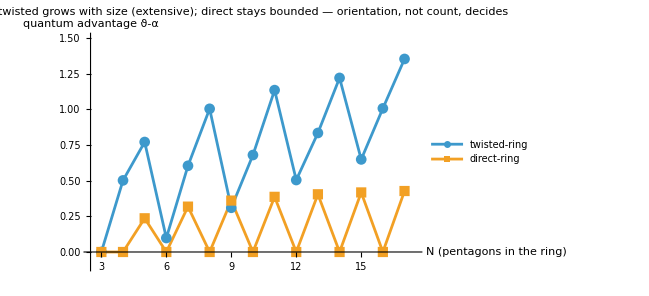

```mathematica
ListLinePlot[{Transpose[{Range[3, 17], {0., 0.5014, 0.7702, 0.0979, 0.6037, 1.0028, 0.3097, 0.6792, 1.1336, 0.5041, 0.8336, 1.2191, 0.6484, 1.0058, 1.3519}}], Transpose[{Range[3, 17], {0., 0., 0.2361, 0., 0.3177, 0., 0.3601, 0., 0.3863, 0., 0.4042, 0., 0.4171, 0., 0.427}}]}, PlotMarkers -> Automatic, PlotLegends -> {"twisted-ring", "direct-ring"}, AxesLabel -> {"N (pentagons in the ring)", "quantum advantage ϑ-α"}, PlotRange -> {{2.5, 17.5}, {-0.1, 1.5}}, ImageSize -> 480, ImagePadding -> {{45, 15}, {40, 28}}, PlotLabel -> "twisted grows with size (extensive); direct stays bounded — orientation, not count, decides"]
```

The growing, upper curve is the twisted ring, extensive by the proof above; the curve pinned near zero at every even N and converging to 1/2 at odd N is the direct ring, bounded by the same proof — neither curve's shape is incidental.

Before searching over words, the whole construction deserves one anatomical summary — and its numbers a live audit. Three layers must be kept distinct. INPUT: one letter per joint, an element of Z_2 — exactly the residual freedom of a pinned edge counted earlier; the letter only decides which endpoint of the shared edge precedes the next block's first own vertex. OBJECT: gluing is identification, not wiring — each joint merges one rim edge of pentagon k with the base edge of pentagon k+1 into a single edge belonging to both 5-cycles, so a length-L word builds ONE exclusivity graph of 3L vertices and 4L edges, not L graphs connected by anything. OUTPUT: α and ϑ are invariants of that whole graph, and they behave asymmetrically: α can be reached from the letters alone, through a 3-state max-plus transfer dynamic program whose matrix product factors along the word (the same transfer matrices that certify the optimality lemmas in the concluding remarks), while ϑ admits no per-letter law at all — it must be paid for with one semidefinite program over all vertices jointly. That asymmetry is the engine of everything that follows: it is why the classical side of every gap in this essay is exact while the quantum side is a certificate. The anchors below are computed live, and the same set was cross-checked independently in Python (networkx + an SCS exactness pass, 16 of 16 checks):

Audit the anatomy live: the α staircase (8 at L = 6, 12 at L = 9 — 4 per 3 blocks), the max-plus factorization trace(T_d T_d T_t T_d T_d T_t) = α, the ϑ SDP reproducing Sqrt[5] on C5 and the chordal anchor 8.347042185 on (ddt)^2, and the direct-ring collapse ϑ = α = 9 already at L = 6:

```mathematica
Module[{wordRing, lovaszTheta, dpS, dpT, mpMul, word6, g6, g9, gT, gD, alpha6, alpha9, alphaT, alphaD, witness, theta5, theta6, thetaT, thetaD, dpTrace, tauStar, gapsAsym, gapsLive, checks}, wordRing[word_String, reps_Integer] := Module[{w = Characters[StringRepeat[word, reps]], L, edges = {}, u, v, km}, L = Length[w]; Do[km = Mod[k - 1, L]; {u, v} = If[w[[km + 1]] === "d", {3*km + 1, 3*km + 2}, {3*km + 2, 3*km + 1}]; edges = Join[edges, {{u, v}, {u, 3*k + 1}, {3*k + 1, 3*k + 2}, {3*k + 2, 3*k + 3}, {3*k + 3, v}}], {k, 0, L - 1}]; Graph[Range[3*L], UndirectedEdge @@@ DeleteDuplicates[Sort /@ edges]]]; lovaszTheta[g_Graph] := Module[{h = IndexGraph[g], n, x, X, vars, cons, sol}, n = VertexCount[h]; X = Table[If[i <= j, x[i, j], x[j, i]], {i, n}, {j, n}]; vars = Flatten[Table[x[i, j], {i, n}, {j, i, n}]]; cons = Join[{Tr[X] == 1, VectorGreaterEqual[{X, 0}, {"SemidefiniteCone", n}]}, (x[#1[[1]], #1[[2]]] == 0 & ) /@ Sort /@ List @@@ EdgeList[h]]; sol = SemidefiniteOptimization[-Total[X, 2], cons, vars, MaxIterations -> 300]; Total[X, 2] /. sol]; dpS = {{0, 0}, {1, 0}, {0, 1}}; dpT[letter_] := Module[{T = ConstantArray[-Infinity, {3, 3}], out, j}, Do[If[ !(dpS[[i,1]] == 1 && s1 == 1) &&  !(s1 == 1 && s2 == 1) &&  !(s2 == 1 && s3 == 1) &&  !(s3 == 1 && dpS[[i,2]] == 1), out = If[letter === "d", {s1, s2}, {s2, s1}]; j = Position[dpS, out][[1,1]]; T[[i,j]] = Max[T[[i,j]], s1 + s2 + s3]], {i, 3}, {s1, 0, 1}, {s2, 0, 1}, {s3, 0, 1}]; T]; mpMul[A_, B_] := Table[Max[Table[A[[i,k]] + B[[k,j]], {k, 3}]], {i, 3}, {j, 3}]; word6 = Characters["ddtddt"]; g6 = wordRing["ddt", 2]; g9 = wordRing["ddt", 3]; gT = wordRing["ttt", 2]; gD = wordRing["ddd", 2]; alpha6 = Length[First[FindIndependentVertexSet[g6]]]; alpha9 = Length[First[FindIndependentVertexSet[g9]]]; alphaT = Length[First[FindIndependentVertexSet[gT]]]; alphaD = Length[First[FindIndependentVertexSet[gD]]]; witness = First[FindIndependentVertexSet[g6]]; theta5 = lovaszTheta[CycleGraph[5]]; theta6 = lovaszTheta[g6]; thetaT = lovaszTheta[gT]; thetaD = lovaszTheta[gD]; dpTrace = Max[Diagonal[Fold[mpMul, dpT[First[word6]], dpT /@ Rest[word6]]]]; tauStar = N[Root[49*#1^3 - 128*#1^2 - 75*#1 + 218 & , 2], 12]; gapsAsym = {0., N[tauStar] - 4/3, 1.40323087 - 4/3}; gapsLive = {thetaD/6 - alphaD/6, thetaT/6 - alphaT/6, theta6/6 - alpha6/6}; checks = {alpha6 == 8, alpha9 == 12, dpTrace == alpha6, alphaT == 8 && alphaD == 9, Abs[theta5 - Sqrt[5.]] < 10^(-5), Abs[theta6 - 8.347042185] < 10^(-3), Abs[thetaD - 9.] < 10^(-3), IndependentVertexSetQ[g6, witness]}; Association["alpha(ddt^2)" -> alpha6, "alpha(ddt^3)" -> alpha9, "maxplus trace of TdTdTtTdTdTt" -> dpTrace, "theta(C5)" -> theta5, "theta(ddt^2)" -> theta6, "theta(ttt^2)" -> thetaT, "theta(ddd^2)" -> thetaD, "witness" -> witness, "gapsLive" -> gapsLive, "gapsAsym" -> gapsAsym, "all 8 anchor checks pass" -> AllTrue[checks, TrueQ]]]
```

<|alpha(ddt^2)→8,alpha(ddt^3)→12,maxplus trace of TdTdTtTdTdTt→8,theta(C5)→2.23607,theta(ddt^2)→8.34704,theta(ttt^2)→8.09789,theta(ddd^2)→9.,witness→{3,4,6,9,10,12,15,17},gapsLive→{-3.53825×10^-9,0.0163149,0.0578404},gapsAsym→{0.,0.0433844,0.0698975},all 8 anchor checks pass→True|>

Assemble all three layers into one picture — the two actions close up, the one graph that W = (ddt)^2 builds, the two invariants computed on it (a maximum independent set drawn filled; the delocalized ϑ witness as a halo), and the resulting gap densities, with live L = 6 readings against the asymptotics:

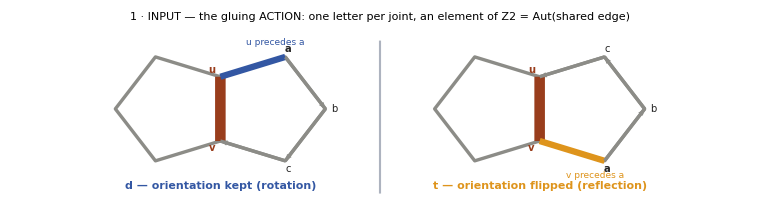
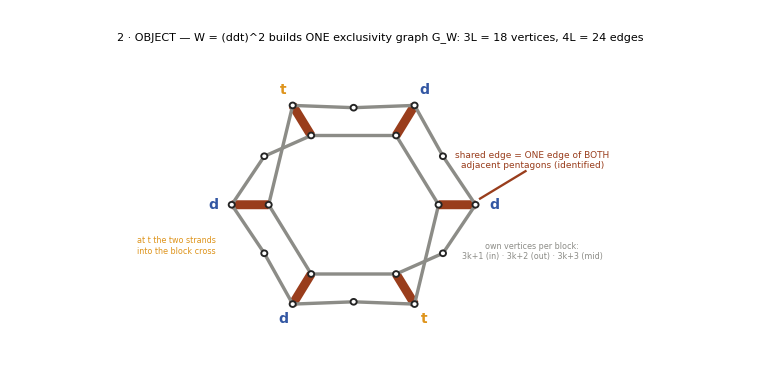
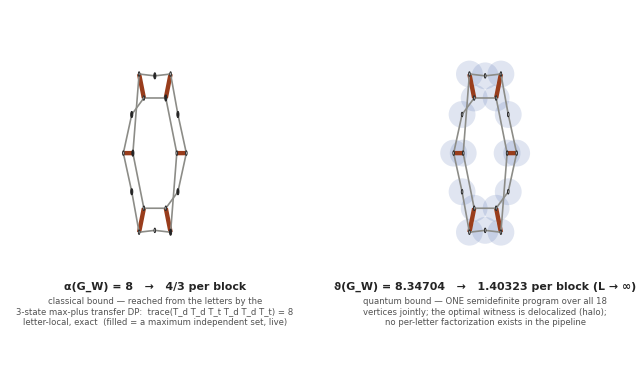
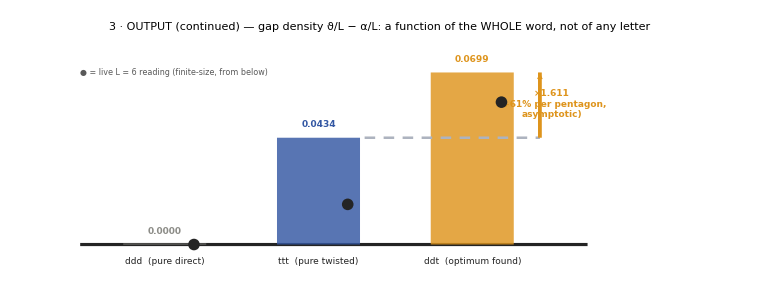
Anatomy of the pentagon mesh — action, object, invariant
-Graphics-
↓   gluing = IDENTIFICATION (quotient): the coral edge is one edge of both blocks — pentagons overlap, they are not wired together
-Graphics-
↓   invariants live on the WHOLE composite graph — α composes letter-by-letter (transfer DP), ϑ does not (global SDP only)
-Graphics-
-Graphics-

```mathematica
Module[{vals, word6, edges6, coral, cAct, cOpt, cLine, gray, ink, pentLpts, pentRpts, jointCloseup, panelIn, rIn, rOut, rMid, rTag, posV, sharedQ, necklacePrims, letterPrims, panelObj, gAlpha, gTheta, gapsAsym, gapsLive, barLabs, barCols, panelBars}, vals = glueAnatomyValues[]; word6 = Characters["ddtddt"]; edges6 = Module[{w = word6, L = 6, edges = {}, u, v, km}, Do[km = Mod[k - 1, L]; {u, v} = If[w[[km + 1]] === "d", {3*km + 1, 3*km + 2}, {3*km + 2, 3*km + 1}]; edges = Join[edges, {{u, v}, {u, 3*k + 1}, {3*k + 1, 3*k + 2}, {3*k + 2, 3*k + 3}, {3*k + 3, v}}], {k, 0, L - 1}]; DeleteDuplicates[Sort /@ edges]]; coral = RGBColor[0.6, 0.24, 0.11]; cAct = RGBColor[0.2, 0.34, 0.64]; cOpt = RGBColor[0.87, 0.58, 0.11]; cLine = RGBColor[0.68, 0.7, 0.75]; gray = RGBColor[0.55, 0.55, 0.53]; ink = GrayLevel[0.14]; pentLpts = Table[{-0.809 + Cos[a*Degree], Sin[a*Degree]}, {a, {36, 108, 180, 252, 324}}]; pentRpts = Table[{0.809 - Cos[a*Degree], Sin[a*Degree]}, {a, {36, 108, 180, 252, 324}}]; jointCloseup[letter_String, xoff_] := Module[{sh = {xoff, 0}, L5, R5, U, V, a, b, c, entry, capCol}, L5 = (#1 + sh & ) /@ pentLpts; R5 = (#1 + sh & ) /@ pentRpts; U = L5[[1]]; V = L5[[5]]; b = R5[[3]]; {a, c} = If[letter === "d", {R5[[2]], R5[[4]]}, {R5[[4]], R5[[2]]}]; entry = If[letter === "d", U, V]; capCol = If[letter === "d", cAct, cOpt]; {CapForm["Round"], JoinForm["Round"], {gray, Thickness[0.0032], Line[Append[L5, L5[[1]]]], Line[Append[R5, R5[[1]]]]}, {coral, Thickness[0.01], Line[{U, V}]}, Text[Style["u", 10, coral, Bold], U + {-0.14, 0.13}], Text[Style["v", 10, coral, Bold], V + {-0.14, -0.13}], {capCol, Thickness[0.006], Arrowheads[{{0.045, 0.62}}], Arrow[{entry, a}]}, {gray, Thickness[0.0032], Arrowheads[{{0.03, 0.58}}], Arrow[{a, b}], Arrow[{b, c}], Arrow[{c, If[letter === "d", V, U]}]}, Text[Style["a", 10, ink, Bold], a + 0.16*Normalize[a - (sh + {0.809, 0})]], Text[Style["b", 10, ink], b + {0.15, 0}], Text[Style["c", 10, ink], c + 0.16*Normalize[c - (sh + {0.809, 0})]], Text[Style[If[letter === "d", "u precedes a", "v precedes a"], 9, capCol, Italic], sh + {0.95, If[letter === "d", 1.22, -1.22]}], Text[Style[If[letter === "d", "d — orientation kept (rotation)", "t — orientation flipped (reflection)"], 11, capCol, Bold], sh + {0, -1.42}]}]; panelIn = Graphics[{jointCloseup["d", -2.75], jointCloseup["t", 2.75], {cLine, Thickness[0.002], Line[{{0, -1.55}, {0, 1.25}}]}}, PlotRange -> {{-5.35, 5.35}, {-1.72, 1.42}}, ImageSize -> 760, PlotLabel -> Style["1 · INPUT — the gluing ACTION: one letter per joint, an element of Z2 = Aut(shared edge)", 12, ink, Bold], ImagePadding -> {{8, 8}, {6, 24}}, Background -> White]; rIn = 1.45; rOut = 2.08; rMid = 1.76; rTag = 2.4; posV[m_] := Module[{k = Quotient[m - 1, 3], aa}, Switch[Mod[m, 3], 1, aa = Pi*(k/3); rIn*{Cos[aa], Sin[aa]}, 2, aa = Pi*(k/3); rOut*{Cos[aa], Sin[aa]}, 0, aa = Pi*(k/3) - Pi/6; rMid*{Cos[aa], Sin[aa]}]]; sharedQ[e_] := Mod[e[[1]], 3] == 1 && e[[2]] == e[[1]] + 1; necklacePrims[fillSet_List, haloQ_] := Join[{CapForm["Round"], JoinForm["Round"]}, If[haloQ, {{Opacity[0.15], cAct, PointSize[0.052], Point[posV /@ Range[18]]}}, {}], Table[With[{e = edges6[[i]]}, If[sharedQ[e], {coral, Thickness[0.0085], Line[{posV[e[[1]]], posV[e[[2]]]}]}, {gray, Thickness[0.0032], Line[{posV[e[[1]]], posV[e[[2]]]}]}]], {i, Length[edges6]}], Table[With[{p = posV[m]}, If[MemberQ[fillSet, m], {FaceForm[ink], EdgeForm[{ink, Thickness[0.0018]}], Disk[p, 0.07]}, {FaceForm[White], EdgeForm[{ink, Thickness[0.0018]}], Disk[p, 0.052]}]], {m, 18}]]; letterPrims = Table[With[{aa = Pi*(j/3), ch = word6[[j + 1]]}, Text[Style[ch, 14, Bold, If[ch === "t", cOpt, cAct]], rTag*{Cos[aa], Sin[aa]}]], {j, 0, 5}]; panelObj = Graphics[Join[necklacePrims[{}, False], letterPrims, {{coral, Thickness[0.0022], Line[{{2.95, 0.62}, {2.14, 0.1}}]}, Text[Style["shared edge = ONE edge of BOTH\nadjacent pentagons (identified)", 9, coral], {3.05, 0.8}, {-1, 0}], Text[Style["own vertices per block:\n3k+1 (in) · 3k+2 (out) · 3k+3 (mid)", 8, gray], {3.05, -0.85}, {-1, 0}], Text[Style["at t the two strands\ninto the block cross", 8, cOpt, Italic], {-3.02, -0.75}, {1, 0}]}], PlotRange -> {{-4.85, 5.75}, {-2.72, 2.72}}, ImageSize -> 760, PlotLabel -> Style["2 · OBJECT — W = (ddt)^2 builds ONE exclusivity graph G_W: 3L = 18 vertices, 4L = 24 edges", 12, ink, Bold], ImagePadding -> {{8, 8}, {6, 24}}, Background -> White]; gAlpha = Graphics[Join[necklacePrims[vals["witness"], False], {Text[Style[Row[{"α(G_W) = ", vals["alpha(ddt^2)"], "   →   4/3 per block"}], 11, ink, Bold], {0, -3.05}], Text[Style["classical bound — reached from the letters by the\n3-state max-plus transfer DP:  trace(T_d T_d T_t T_d T_d T_t) = 8\nletter-local, exact  (filled = a maximum independent set, live)", 8.5, GrayLevel[0.32]], {0, -3.62}]}], PlotRange -> {{-2.95, 2.95}, {-4.15, 2.72}}, ImageSize -> 372, Background -> White]; gTheta = Graphics[Join[necklacePrims[{}, True], {Text[Style[Row[{"ϑ(G_W) = ", NumberForm[vals["theta(ddt^2)"], {8, 5}], "   →   1.40323 per block (L → ∞)"}], 11, ink, Bold], {0, -3.05}], Text[Style["quantum bound — ONE semidefinite program over all 18\nvertices jointly; the optimal witness is delocalized (halo);\nno per-letter factorization exists in the pipeline", 8.5, GrayLevel[0.32]], {0, -3.62}]}], PlotRange -> {{-2.95, 2.95}, {-4.15, 2.72}}, ImageSize -> 372, Background -> White]; gapsAsym = vals["gapsAsym"]; gapsLive = vals["gapsLive"]; barLabs = {"ddd  (pure direct)", "ttt  (pure twisted)", "ddt  (optimum found)"}; barCols = {gray, cAct, cOpt}; panelBars = Graphics[{CapForm["Round"], JoinForm["Round"], {ink, Thickness[0.003], Line[{{0.45, 0}, {3.75, 0}}]}, Table[{barCols[[i]], Opacity[0.82], Rectangle[{i - 0.27, 0}, {i + 0.27, Max[gapsAsym[[i]], 0.0004]}]}, {i, 3}], Table[Text[Style[NumberForm[gapsAsym[[i]], {5, 4}], 9, barCols[[i]], Bold], {i, gapsAsym[[i]] + 0.0052}], {i, 3}], Table[Text[Style[barLabs[[i]], 9, ink], {i, -0.0068}], {i, 3}], Table[{ink, PointSize[0.011], Point[{i + 0.19, Max[gapsLive[[i]], 0.]}]}, {i, 3}], Text[Style["● = live L = 6 reading (finite-size, from below)", 8, GrayLevel[0.35]], {1.06, 0.07}, {-1, 0}], {cLine, Dashing[{0.01, 0.008}], Thickness[0.0024], Line[{{2.3, gapsAsym[[2]]}, {3.44, gapsAsym[[2]]}}]}, {cOpt, Thickness[0.0036], Arrowheads[0.028], Arrow[{{3.44, gapsAsym[[2]]}, {3.44, gapsAsym[[3]]}}]}, Text[Style["×1.611\n(+61% per pentagon,\nasymptotic)", 9, cOpt, Bold], {3.52, 0.057}, {-1, 0}]}, PlotRange -> {{0.38, 4.42}, {-0.013, 0.082}}, AspectRatio -> 0.4, ImageSize -> 760, PlotLabel -> Style["3 · OUTPUT (continued) — gap density ϑ/L − α/L: a function of the WHOLE word, not of any letter", 12, ink, Bold], ImagePadding -> {{8, 8}, {6, 24}}, Background -> White]; Column[{Style["Anatomy of the pentagon mesh — action, object, invariant", 15, ink, Bold], panelIn, Style["↓   gluing = IDENTIFICATION (quotient): the coral edge is one edge of both blocks — pentagons overlap, they are not wired together", 9.5, GrayLevel[0.35], Italic], panelObj, Style["↓   invariants live on the WHOLE composite graph — α composes letter-by-letter (transfer DP), ϑ does not (global SDP only)", 9.5, GrayLevel[0.35], Italic], GraphicsRow[{gAlpha, gTheta}], panelBars}, Spacings -> 1., Alignment -> Center]]
```

## Searching for the Optimal Word: ddt

Neither pure orientation turns out to be optimal. Treating the ring as built from an infinite repeating word over the alphabet {d, t} — one letter per gluing joint — and searching over words rather than only the two pure orientations, the word (ddt)∞ (two direct joints, one twisted, repeated) was found to keep more quantum advantage per pentagon than pure twisted, by about 61%: gap(ddt) = 0.0698975… against gap(twisted) = τ* − 4/3 ≈ 0.043384. A slice of the mesh this word builds, glued into a closed ring — each block's own drawn orientation below is the real cumulative R_direct/R_twisted parity, not a schematic stand-in:

Build the 51-pentagon ddt necklace; a block is drawn mirrored exactly when an odd number of twisted joints precede it:

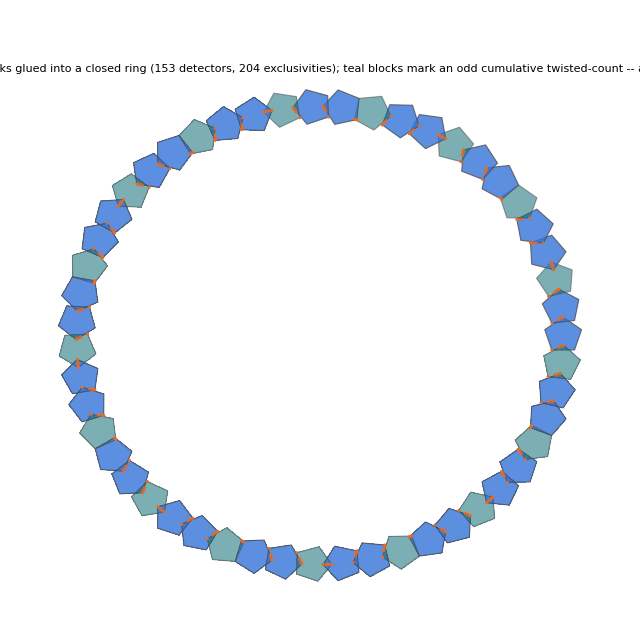

```mathematica
Module[{letters, np, rad, cumTwistedCount, mirrorQ, localPenta, centers, pentagons, joints, coral, cDirect, cTwisted}, letters = Characters[StringRepeat["ddt", 17]]; np = Length[letters]; rad = 0.62*(np/(2*Pi)); cumTwistedCount = FoldList[Plus, 0, (Boole[#1 === "t"] & ) /@ letters][[1 ;; np]]; mirrorQ[k_] := OddQ[cumTwistedCount[[k + 1]]]; localPenta[mirror_] := Table[{Cos[2*Pi*(j/5) + Pi/2], If[mirror, -1, 1]*Sin[2*Pi*(j/5) + Pi/2]}, {j, 0, 4}]; centers = Table[rad*{Cos[2*Pi*(k/np)], Sin[2*Pi*(k/np)]}, {k, 0, np - 1}]; pentagons = Table[(centers[[k + 1]] + 0.4*RotationTransform[2*Pi*(k/np)][#1] & ) /@ localPenta[mirrorQ[k]], {k, 0, np - 1}]; joints = Table[Module[{a = pentagons[[k + 1]], b = pentagons[[Mod[k + 1, np] + 1]], ja, jb}, ja = First[SortBy[a, EuclideanDistance[#1, Mean[b]] & ]]; jb = First[SortBy[b, EuclideanDistance[#1, Mean[a]] & ]]; {ja, jb}], {k, 0, np - 1}]; coral = RGBColor[0.9, 0.42, 0.15]; cDirect = RGBColor[0.2, 0.45, 0.85]; cTwisted = RGBColor[0.06, 0.43, 0.46]; Graphics[{Table[{If[letters[[k + 1]] == "d", cDirect, cTwisted], Opacity[If[letters[[k + 1]] == "d", 0.8, 0.55]], EdgeForm[GrayLevel[0.3]], Polygon[pentagons[[k + 1]]]}, {k, 0, np - 1}], {coral, Opacity[0.85], Thickness[0.0035], Dashed, Line /@ joints}, {coral, PointSize[0.0035], Point[Flatten[joints, 1]]}}, ImageSize -> 640, PlotRange -> All, AspectRatio -> Automatic, PlotLabel -> "a ddt necklace at scale: 51 pentagon blocks glued into a closed ring (153 detectors, 204 exclusivities); teal blocks mark an odd cumulative twisted-count -- a genuine reflection, not a decorative rotation"]]
```

A 180-degree rotation and a reflection are not the same operation — one preserves orientation (det = +1), the other reverses it (det = -1) — so the mirrored (teal) blocks above are drawn as actual mirror images, not rotated copies. That mirror pattern is the sign of an accumulated matrix, not an artistic choice: composing R_direct or R_twisted once per joint from block 0 up to block k gives a matrix M_k, and the block is mirrored exactly when Det[M_k] = -1. Confirmed three independent ways at 60-digit precision — the raw 51-fold matrix product; that same product's exact factorization as the already-verified 3-gate (ddt) unit cell (the circuit two subsections above) raised to the 17th power; and an actual 51-gate QuantumCircuitOperator built from real qutrit gates, through the Wolfram Quantum Computation Framework:

```mathematica
Module[{letters, Rdirect, Rtwisted, gateOf, unitCell, gates, circuit, rawProduct}, letters = Characters[StringRepeat["ddt", 17]]; Rdirect = N[RotationMatrix[4*(Pi/5), {1, 0, 0}], 60]; Rtwisted = DiagonalMatrix[{1, 1, -1}] . Rdirect; gateOf[l_] := If[l === "d", Rdirect, Rtwisted]; rawProduct = Fold[gateOf[#2] . #1 & , IdentityMatrix[3], letters]; unitCell = Rtwisted . Rdirect . Rdirect; gates = (QuantumOperator[gateOf[#1], 3] & ) /@ letters; circuit = QuantumCircuitOperator[gates]; {circuit["UnitaryQ"], Chop[Det[circuit["Matrix"]] + 1, 10^(-25)] == 0, Chop[MatrixPower[unitCell, 17] - rawProduct, 10^(-25)] == ConstantArray[0, {3, 3}], Chop[circuit["Matrix"] - rawProduct, 10^(-25)] == ConstantArray[0, {3, 3}]}]
```

{True,True,True,True}

All four checks hold: the 51-gate circuit is unitary, its net determinant is exactly -1 (17 twisted joints, an odd number), and both independent cross-checks match the raw product exactly — the drawn necklace, the algebraic unit-cell power, and the actual quantum circuit are three views of the same computation, not three separate claims.

The necklace computation just verified has a classical name, and the name organizes everything this section has built. Label each joint of the base ring with its matrix — R_direct or R_twisted: in combinatorics a group-labeled graph is a voltage (gain) graph; in geometry the same data is a flat O(3)-bundle over the ring, presented by its gluing data — the descent formalism that assembles a manifold from charts or a gauge field from local trivializations (in physics dialect: a Z_2 lattice gauge field, whose Wilson loop is exactly the product above). The accumulated matrix around the ring — the 51-fold product — is the bundle's holonomy, and its determinant sign (-1)^#twisted is the complete topological invariant of the gluing pattern: the first Stiefel–Whitney class w_1 in H^1(ring; Z_2). Even twisted-count is the trivial class — the cylinder; odd is the nontrivial one — the Möbius band. The dichotomy is not an analogy: delete the glue rails from the glued graph itself and the surviving strands close into two separate loops exactly when the twisted-count is even (for the pure-direct ring they are precisely the C_N and C_2N of the theorem above), and into the Möbius band's single boundary loop exactly when it is odd. Two facts keep the framing honest. First, the gauge moves of the Z_2 data — re-orienting one block's local frame, which flips the parity label at its two adjacent joints — collapse all 2^L parity words of a given length into exactly two classes, so at the level of bundle topology the parity is all that survives of a gluing word. Second, the Lovász densities are not functions of that class: ddt and pure twisted lie in the same Möbius class yet have different gap densities. Topology decides orientability; the optimization problem of the closing sections lives in the finer geometry above it — one more way of seeing why no coarse invariant settles it:

Verify each level live: the cohomology count (all 64 length-6 parity words, coboundary flips at every block, exactly two gauge classes, separated by holonomy parity); the boundary-strand test on the glued graphs themselves (delete the glue rails and count the surviving loops — checked for every word of length ≤ 4, then on the pure-direct, pure-twisted and ddt rings); and the exact holonomy determinant of the 51-joint ddt necklace:

```mathematica
Module[{flips, coboundaries, orbits, parityInvariantQ, strandCount, strandRuleQ, ringStrands, Rd, Rt, unitDet, gapDdt, gapTwisted}, flips = Table[ReplacePart[ConstantArray[0, 6], {k -> 1, Mod[k, 6] + 1 -> 1}], {k, 6}]; coboundaries = DeleteDuplicates[Table[Mod[s . flips, 2], {s, Tuples[{0, 1}, 6]}]]; orbits = DeleteDuplicates[Table[Sort[(Mod[w + #1, 2] & ) /@ coboundaries], {w, Tuples[{0, 1}, 6]}]]; parityInvariantQ = Sort[Table[DeleteDuplicates[Mod[Total /@ orb, 2]], {orb, orbits}]] === {{0}, {1}}; strandCount[word_String, reps_Integer] := Module[{w, L, u, v, km, edges, rails}, w = Characters[StringRepeat[word, reps]]; L = Length[w]; edges = Flatten[Table[km = Mod[k - 1, L]; {u, v} = If[w[[km + 1]] === "d", {3*km + 1, 3*km + 2}, {3*km + 2, 3*km + 1}]; {{u, v}, {u, 3*k + 1}, {3*k + 1, 3*k + 2}, {3*k + 2, 3*k + 3}, {3*k + 3, v}}, {k, 0, L - 1}], 1]; rails = Table[{3*k + 1, 3*k + 2}, {k, 0, L - 1}]; Length[ConnectedComponents[Graph[Range[3*L], UndirectedEdge @@@ Complement[DeleteDuplicates[Sort /@ edges], rails]]]]]; strandRuleQ = AllTrue[Flatten[Table[StringJoin /@ Tuples[{"d", "t"}, len], {len, 1, 4}]], strandCount[#1, 3] == If[EvenQ[3*StringCount[#1, "t"]], 2, 1] & ]; ringStrands = {"d" -> strandCount["d", 17], "t" -> strandCount["t", 17], "ddt" -> strandCount["ddt", 17]}; Rd = RotationMatrix[4*(Pi/5), {1, 0, 0}]; Rt = DiagonalMatrix[{1, 1, -1}] . Rd; unitDet = FullSimplify[Det[Rt . Rd . Rd]]; gapDdt = 1.40323087 - 4/3; gapTwisted = N[Root[49*#1^3 - 128*#1^2 - 75*#1 + 218 & , 2] - 4/3]; Association["H1(C6;Z2): gauge classes among all 64 length-6 parity words" -> Length[orbits], "  class invariant is exactly the holonomy parity (-1)^#t" -> parityInvariantQ, "glue rails deleted: 2 strand loops iff #t even, 1 iff odd (all words, len <= 4)" -> strandRuleQ, "  this essay's rings: pure direct, pure twisted, ddt" -> ringStrands, "exact det of the ddt unit cell, and of the 51-joint necklace holonomy" -> {unitDet, unitDet^17}, "ddt vs pure twisted: same w1 class, yet different gap density" -> {OddQ[StringCount["ddt", "t"]] == OddQ[StringCount["ttt", "t"]], {gapDdt, gapTwisted}}]]
```

<|H1(C6;Z2): gauge classes among all 64 length-6 parity words→2,  class invariant is exactly the holonomy parity (-1)^#t→True,glue rails deleted: 2 strand loops iff #t even, 1 iff odd (all words, len <= 4)→True,  this essay's rings: pure direct, pure twisted, ddt→{d→2,t→1,ddt→1},exact det of the ddt unit cell, and of the 51-joint necklace holonomy→{-1,-1},ddt vs pure twisted: same w1 class, yet different gap density→{True,{0.0698975,0.0433844}}|>

Measured as the quantum advantage contributed per pentagon (the gap density), the three strategies compare as follows:

Compare the cited gap density per pentagon across the three strategies:

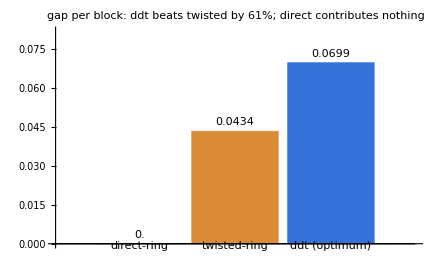

```mathematica
BarChart[{0., 0.0433844, 0.0698975}, ChartLabels -> {"direct-ring", "twisted-ring", "ddt (optimum)"}, ChartStyle -> {GrayLevel[0.72], RGBColor[0.85, 0.55, 0.2], RGBColor[0.2, 0.45, 0.85]}, PlotRange -> {0, 0.082}, ImageSize -> 440, ImagePadding -> {{48, 20}, {46, 36}}, LabelingFunction -> (Placed[NumberForm[#1, 3], Above] & ), PlotLabel -> "gap per block: ddt beats twisted by 61%; direct contributes nothing"]
```

## Why This Resists Proof: De Bruijn Graphs and Ergodic Optimization

Confirming that ddt really is the best of ALL infinite gluing words — not just the best among the words actually tried — is a different kind of problem: an ergodic-optimization (mean-payoff / joint-spectral-radius) problem over the shift space of {d,t}-sequences. Every length-k window of that shift space is a node of a de Bruijn graph, read one letter at a time; a periodic gluing word is exactly a cycle in that graph, and (ddt)∞ is precisely the 3-cycle ddt → dtd → tdd → ddt:

Build the de Bruijn-3 graph over {d,t}, highlighting the ddt orbit, with the direct/twisted rotation-vs-reflection pair recapped below it for reference:

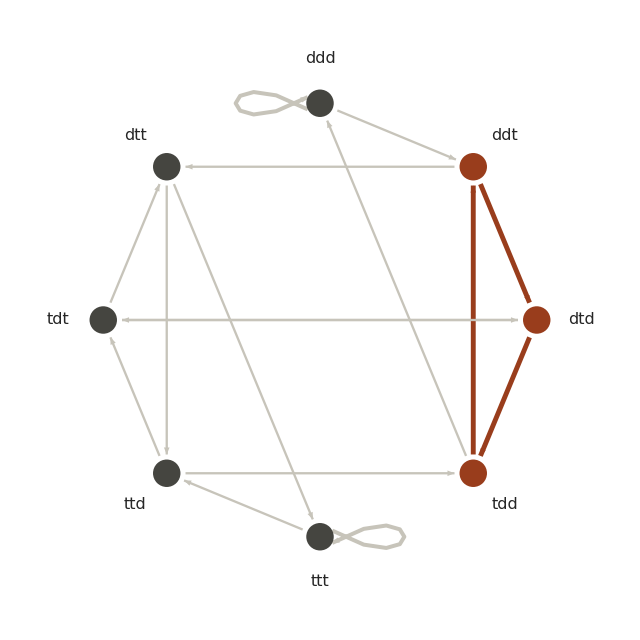
-Graphics-
-Graphics-

```mathematica
Module[{coral, grayN, grayLine, ink, verts, R, nodeR, labelR, angles, pos, labelPos, edgeList, hlEdgeQ, hlNodeQ, trimLine, edgeGr, nodeGr, labelGr, deBruijnGraphic, directTwistedSmall}, coral = RGBColor[0.6, 0.24, 0.11]; grayN = RGBColor[0.27, 0.27, 0.25]; grayLine = RGBColor[0.78, 0.77, 0.73]; ink = GrayLevel[0.15]; verts = {"ddd", "ddt", "dtd", "tdd", "ttt", "ttd", "tdt", "dtt"}; R = 3; nodeR = 0.19; labelR = R + 0.62; angles = Table[(90 - 45*k)*Degree, {k, 0, 7}]; pos = AssociationThread[verts, Table[R*{Cos[a], Sin[a]}, {a, angles}]]; labelPos = AssociationThread[verts, Table[labelR*{Cos[a], Sin[a]}, {a, angles}]]; edgeList = {{"ddd", "ddd"}, {"ddd", "ddt"}, {"ddt", "dtd"}, {"ddt", "dtt"}, {"dtd", "tdd"}, {"dtd", "tdt"}, {"dtt", "ttd"}, {"dtt", "ttt"}, {"tdd", "ddd"}, {"tdd", "ddt"}, {"tdt", "dtd"}, {"tdt", "dtt"}, {"ttd", "tdd"}, {"ttd", "tdt"}, {"ttt", "ttd"}, {"ttt", "ttt"}}; hlEdgeQ[{a_, b_}] := MemberQ[{{"ddt", "dtd"}, {"dtd", "tdd"}, {"tdd", "ddt"}}, {a, b}]; hlNodeQ[v_] := MemberQ[{"ddt", "dtd", "tdd"}, v]; trimLine[a_, b_, gap_:0.26] := Module[{pa = pos[a], pb = pos[b], u}, u = (pb - pa)/Norm[pb - pa]; {pa + gap*u, pb - gap*u}]; edgeGr = Table[If[e[[1]] == e[[2]], Module[{p = pos[e[[1]]], dir, perp, p1, p2, c1, c2}, dir = p/Norm[p]; perp = {-dir[[2]], dir[[1]]}; p1 = p + nodeR*Normalize[perp - 0.5*dir]; p2 = p + nodeR*Normalize[perp + 0.5*dir]; c1 = p + 1.5*(perp + 0.45*dir); c2 = p + 1.5*(perp - 0.45*dir); {grayLine, Thickness[0.0045], Arrowheads[0.05], Arrow[BezierCurve[{p1, c1, c2, p2}]]}], Module[{ab = trimLine[e[[1]], e[[2]]]}, {If[hlEdgeQ[e], coral, grayLine], Thickness[If[hlEdgeQ[e], 0.0055, 0.0026]], Arrowheads[If[hlEdgeQ[e], 0.03, 0.02]], Arrow[ab]}]], {e, edgeList}]; nodeGr = Table[{If[hlNodeQ[v], coral, grayN], Disk[pos[v], nodeR]}, {v, verts}]; labelGr = Table[Text[Style[v, 16, ink], labelPos[v]], {v, verts}]; deBruijnGraphic = Graphics[{edgeGr, nodeGr, labelGr}, PlotRange -> 4.35, ImageSize -> 640, ImagePadding -> {{20, 20}, {15, 15}}, Background -> White]; directTwistedSmall = Rasterize[Show[fig2[], ImagePadding -> {{10, 10}, {10, 10}}], ImageSize -> 380]; Column[{deBruijnGraphic, directTwistedSmall}, Spacings -> 0.3, Alignment -> Center]]
```

Certificates built on de Bruijn graphs of increasing window size k give successively tighter upper bounds Γ_k on the best possible gap density attainable by ANY gluing word. Every Γ_k computed so far sits strictly above gap(ddt) (the dashed line) — evidence that ddt is close to optimal, and the bound tightens as k grows:

Plot Γ_7..Γ_10 against gap(ddt). Each Γ_k comes from a small semidefinite program: one rational positive-semidefinite block per de Bruijn-k node, assembled edge-by-edge around any ring via a Schur-complement argument into an exact per-block bound on ϑ; minimizing that bound over all valid block choices gives Γ_k as a provable ceiling on the gap density of every word of window size k, periodic or not (the semidefinite program itself is not re-solved live here — only its already-certified output is plotted):

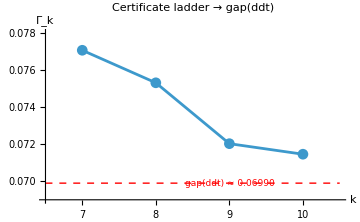

```mathematica
ListLinePlot[{{7, 0.0770624}, {8, 0.0753086}, {9, 0.072026}, {10, 0.0714575}}, PlotMarkers -> Automatic, Joined -> True, Epilog -> {Directive[Red, Dashed], Line[{{6.5, 0.0698975}, {10.5, 0.0698975}}], Text[Style["gap(ddt) ≈ 0.06990", 9], {9, 0.0698975}, {0, -1.4}]}, AxesLabel -> {"k", "Γ_k"}, PlotRange -> {{6.5, 10.5}, {0.069, 0.078}}, PlotLabel -> "Certificate ladder → gap(ddt)", ImageSize -> 360]
```

But the bound never reaches gap(ddt) exactly, and it provably cannot be forced to by this method alone: this class of ergodic-optimization problems is known to fail the “finiteness property” in general (Bousch–Mairesse, 2002) — the true optimal word can, in principle, be a non-periodic (Sturmian) sequence that no search over periodic words, however long, will ever encounter. So no amount of extending this series can, by itself, prove that ddt is the global optimum.

## From Gluing Words to Black-Box Certification

Everything so far is composition mathematics; this closing section is what it is for — and why the essay carries the title it does. Return to the sealed box that opened the first section: a device claims to be quantum, and only its click statistics can be observed. The pentagon is the smallest interrogation protocol whose quantum answer no classical hidden-variable account can match, and the gap ϑ - α is the margin of that impossibility — the certifiable advantage per interrogation round. A mesh is therefore a certification instrument, and its gluing word is a design parameter: it sets how the margin scales with instrument size. Direct rings collapse the margin outright (ϑ = α at even N: a larger instrument with zero statistical power); twisted rings hold a fixed margin of τ* - 4/3 ≈ 0.0434 per pentagon; the ddt word raises it to ≈ 0.0699 — the 61% of the abstract. Optimizing gap density, the business of the preceding sections, is optimizing the statistical power of a black-box test per unit of hardware.

The quantum side of such a test stays remarkably cheap. The twisted-chain bound is realized, at every length, by the same three-level system Lapkiewicz et al. (2011) drove through one pentagon — a single photon on three optical paths; growing the mesh grows only the list of measurement settings, never the dimension. The noise requirement does not run away with size either: under isotropic noise the critical visibility — the signal fraction below which the quantum advantage disappears — rises from 0.5854 for a single pentagon but saturates at 1/(3(τ* - 1)) ≈ 0.8848 in the long-chain limit. A fixed ~88.5% visibility target, independent of instrument size, is an unusually forgiving scaling law for an entanglement-free contextuality experiment.

Both endpoints of that visibility law, exactly — the single-pentagon value and the long-chain ceiling, from the same algebraic τ*:

```mathematica
tauStar = Root[49 #^3 - 128 #^2 - 75 # + 218 &, 2];
{FullSimplify[(2 - 5/3)/(Sqrt[5] - 5/3)], N[(2 - 5/3)/(Sqrt[5] - 5/3), 5],
 N[1/(3 (tauStar - 1)), 5]}
```

{1/20 (5+3 √5),0.58541,0.88484}

Now the title's converse question: could a classical optical device fake the box? On statistics alone the uncomfortable answer is yes, in principle: a classical light beam, split and redistributed with tuned intensities, can reproduce any consistent table of click frequencies — the quantum-optimal one included. That is a theorem, not a defect of imagination, and it has a sharp corollary: no function of the observed table alone can bound what the device's internal dynamics generate. Breaking the tie takes a second, independent lens — audit the dynamics a claimed optical design is even capable of generating. Passive linear optics, the beamsplitters and phase shifters an intensity forger is limited to, close inside the compact algebra u(n), of dimension at most n^2 on n modes; squeezing escapes into the full symplectic algebra sp(2n,R), of dimension n(2n+1). Which side a design falls on is decidable by an exact-arithmetic rank computation, polynomial in the number of modes — in sharp contrast to the qubit-side Lie closure, which grows as 4^n - 1 and stalls at two glued pentagons.

The audit, self-contained — exact iterated-commutator closure of the declared generators in the quadrature representation; staying inside u(n) (every element antisymmetric, dimension ≤ n^2) means the design is reproducible by passive linear optics:

```mathematica
comm[a_, b_] := a . b - b . a;
rk[ms_] := If[ms === {}, 0, MatrixRank[Flatten /@ ms]];
indep[ms_] := Fold[If[rk[Append[#1, #2]] > rk[#1], Append[#1, #2], #1] &, {}, ms];
closure[gens_] :=
  FixedPoint[indep[Join[#, Flatten[Outer[comm, #, #, 1], 1]]] &, indep[gens]];
omega[n_] := KroneckerProduct[IdentityMatrix[n], {{0, 1}, {-1, 0}}];
qf[n_, terms_] := Total[Module[{m = ConstantArray[0, {2 n, 2 n}]},
     m[[#1, #2]] += #3/2; m[[#2, #1]] += #3/2; m] & @@@ terms];
gen[n_, terms_] := omega[n] . qf[n, terms];
phase[n_, j_] := gen[n, {{2 j - 1, 2 j - 1, 1}, {2 j, 2 j, 1}}];
bsRe[n_, j_, k_] := gen[n, {{2 j - 1, 2 k - 1, 1}, {2 j, 2 k, 1}}];
bsIm[n_, j_, k_] := gen[n, {{2 j - 1, 2 k, 1}, {2 j, 2 k - 1, -1}}];
sq1[n_, j_] := gen[n, {{2 j - 1, 2 j - 1, 1}, {2 j, 2 j, -1}}];
sq2Re[n_, j_, k_] := gen[n, {{2 j - 1, 2 k - 1, 1}, {2 j, 2 k, -1}}];
sq2Im[n_, j_, k_] := gen[n, {{2 j - 1, 2 k, 1}, {2 j, 2 k - 1, 1}}];
audit[gens_, n_] := Module[{b = closure[gens]},
   <|"closure dimension" -> rk[b], "u(n) dimension" -> n^2,
    "sp(2n,R) dimension" -> n (2 n + 1),
    "verdict" -> If[AllTrue[b, Transpose[#] === -# &] && rk[b] <= n^2,
      "passive-confined: emulable by linear optics",
      "active: genuine squeezing, beyond passive optics"]|>];
Column[{"passive interferometer, 2 modes (phases + beamsplitter):",
  audit[{phase[2, 1], phase[2, 2], bsRe[2, 1, 2], bsIm[2, 1, 2]}, 2],
  "analogue-Hawking channel (phases + graybody beamsplitter + two-mode squeezer):",
  audit[{phase[2, 1], phase[2, 2], bsRe[2, 1, 2], bsIm[2, 1, 2],
    sq2Re[2, 1, 2], sq2Im[2, 1, 2]}, 2],
  "single squeezed mode (squeezer + phase), 1 mode:",
  audit[{phase[1, 1], sq1[1, 1]}, 1]}, Spacings -> 0.8]
```

passive interferometer, 2 modes (phases + beamsplitter):
<|closure dimension→4,u(n) dimension→4,sp(2n,R) dimension→10,verdict→passive-confined: emulable by linear optics|>
analogue-Hawking channel (phases + graybody beamsplitter + two-mode squeezer):
<|closure dimension→10,u(n) dimension→4,sp(2n,R) dimension→10,verdict→active: genuine squeezing, beyond passive optics|>
single squeezed mode (squeezer + phase), 1 mode:
<|closure dimension→3,u(n) dimension→1,sp(2n,R) dimension→3,verdict→active: genuine squeezing, beyond passive optics|>

Run on three declared designs, the audit returns computed verdicts, not promises: a passive two-mode interferometer stays confined at dimension 4 = u(2) — emulable; add the two-mode squeezer that models a horizon and the closure jumps to dimension 10, all of sp(4,R) — active, beyond any passive-optics emulation; even a single squeezed mode already escapes (dimension 3 = sp(2,R)). The middle row is the program's flagship application under this audit: the analogue-Hawking channel — free phase evolution, graybody backscatter as a beamsplitter, pair production at the horizon as a two-mode squeezer — is certifiably not passive-optics-emulable, even though its correlations, being Gaussian, remain efficiently classically simulable. On that channel the two lenses genuinely part ways, and both are right — which is precisely why the certification battery carries both. Within the class of classical intensity emulators, that battery is moreover provably complete — every such impostor is either distinguished from a genuine quantum device or certified classically bounded — a conditional theorem resting on one stated detector-physics premise.

One verdict is deliberately left unclaimed: the whole-mesh one. Block by block, every pentagon of a glued mesh passes the genuine-side audit — each block carries the same full rotation algebra as the single-pentagon cascade — but a single joint verdict for the composed device would take either the qubit-side closure (out of reach beyond two pentagons: the two-pentagon case already needs roughly 128 GB of memory, three pentagons is terabyte-scale — and, worse, non-discriminating exactly here, since direct and twisted rings share identical closure growth despite opposite gap behavior) or a physically justified optical compilation frame for an arbitrary gluing word, which is new research. The polynomial passive-versus-active audit above is the instrument built for that job. Pointing it at an arbitrary mesh word is the open frontier on the physics side of this essay, standing exactly where the ergodic-optimization conjecture stands on its mathematics side.

## Concluding Remarks

Direct and twisted give exact, opposite-fate closed forms for the two simplest gluing choices; searching over gluing words instead of just these two finds (ddt)∞, and two facts true of every word — not just the ones tried — show it is provably optimal outside a narrow, precisely-bounded window, and a very strong candidate everywhere else. A single minimal atom of contextuality, composed by nothing more than a choice of how to glue its edges together, turns out to hide a genuinely open problem in ergodic optimization.

And the composed object is not an end in itself: as the preceding section makes concrete, a glued mesh is a black-box certification instrument — its gap density the test's statistical power per pentagon, its quantum side a single qutrit at a fixed ~88.5% visibility target, and its classical-emulation question audited by an exact polynomial passive-versus-active criterion, with the whole-mesh verdict standing as the physics-side open frontier.

### The Ceiling and the Floor

Two facts hold for every gluing word at once, periodic or not, and together they close most of the gap the previous section left open. Start with a hard ceiling: no matter which word is chosen, ϑ-bar(W) can never exceed 3/2. The reason is one accounting trick read two ways: spread weight 1/2 over every vertex and that alone is already a fractional packing of value 3/2 per block; spread weight 1/2 instead over each block's two internal edges and its two glue-in edges (leaving the shared edge bare) and that's a fractional edge cover of the exact same value. Squeezed between a packing and a cover of equal size, that value is exact — and since ϑ never exceeds a fractional packing number, neither does ϑ-bar(W).

A second fact is where ddt's real specialness shows up — not in beating twisted, but in what it takes to tie it. For every word, α-bar(W) ≥ max(4/3, 1 + f_d/2), where f_d is the fraction of joints that are direct. Pure twisted (f_d = 0) reaches the 4/3 floor exactly, same as ddt; ddt is singled out only by ALSO maximizing the direct-fraction at f_d = 2/3 while still sitting on that floor — no other word manages both.

A scoring trick proves it in three connected steps, all checked live in one certificate: score each interface state (0, -1/2, -1); every direct or twisted transition then gains at least 3/2 or 1 net of the score change, giving density ≥ 1 + f_d/2 in general; the same scoring, run three direct letters deep, gives a STRICTLY better rate of 13/3 = 3(4/3) + 1/3 — so hitting the floor exactly rules out three direct letters in a row; and at f_d = 2/3 the direct-runs between twisted letters average exactly 2, which, with runs of 3 now forbidden, forces every run to equal exactly 2 — precisely the definition of (ddt)^k:

```mathematica
Module[{phiC = {0, -2^(-1), -1}, phiB = {0, -3^(-1), -2/3}, adjR, Acc, mpMul, A3, comb}, adjR[T_, phi_, i_] := Max[Table[T[[i,j]] + phi[[j]] - phi[[i]], {j, 3}]]; Acc = Table[dpTransfer["d"][[i,j]] + phiB[[j]] - phiB[[i]], {i, 3}, {j, 3}]; mpMul[X_, Y_] := Table[Max[Table[X[[i,k]] + Y[[k,j]], {k, 3}]], {i, 3}, {j, 3}]; A3 = mpMul[mpMul[Acc, Acc], Acc]; comb = AllTrue[Flatten[Table[If[Mod[p, 3] == 0, Module[{ws = Select[Tuples[{"d", "t"}, p], Count[#1, "d"] == 2*(p/3) &&  !StringContainsQ[StringJoin[StringJoin[#1], StringJoin[#1]], "ddd"] & ]}, AllTrue[ws, MemberQ[Table[RotateLeft[Characters[StringRepeat["ddt", p/3]], r], {r, 0, p - 1}], #1] & ]], True], {p, 3, 12}]], TrueQ]; AllTrue[Range[3], adjR[dpTransfer["d"], phiC, #1] >= 3/2 & ] && AllTrue[Range[3], adjR[dpTransfer["t"], phiC, #1] >= 1 & ] && Min[Table[Max[A3[[i]]], {i, 3}]] == 13/3 && comb]
```

True

Put the ceiling and the floor together and the open question shrinks to a narrow strip:

```mathematica
{N[3/2 - (0.0698975), 8], N[0.0714575 - 0.0698975, 6]}
```

{1.4301,0.00156}

The first number is where the ceiling alone already settles things: for α-bar(W) ≥ 1.4301025, ϑ-bar(W) ≤ 3/2 forces gap(W) ≤ 3/2 - α-bar(W) ≤ gap(ddt), so ddt cannot be beaten there — proven, not conjectured. The second is the certificate-ladder residual from the previous section, bounding every OTHER word to within ϵ ≈ 0.0016 of ddt regardless. Between the two, ddt's status is about as settled as a genuinely open problem can be — only the low-classical-density, ddt-like words near the floor are still undecided.

### Future Directions

Four directions follow directly from the boundary of what is proven above:

Close the residual window: ddt's optimality is proven for α-bar(W) ≥ 1.4301025 and certified to within ϵ ≈ 0.0016 elsewhere; the narrow window α-bar(W) ∈ [4/3, 1.4301025) remains open and is the sharpest unresolved piece of the argument.

Rule out, or find, an aperiodic competitor: since the finiteness property can fail by admitting a non-periodic (Sturmian) maximizer, the natural next step is a targeted search or exclusion argument over aperiodic gluing words, not further periodic enumeration.

Tighten the certificate ladder: extending Γ_k to larger window sizes k shrinks ϵ further and narrows the evidence, even though — per the obstruction above — it cannot by itself prove global optimality.

Point the physical lens at the composition: the polynomial passive-versus-active audit of the closing section decides optical emulability for declared designs; extending it to a single joint verdict for a whole glued mesh needs a physically justified optical compilation frame for arbitrary gluing words — the open frontier where this essay's mathematics meets its physics.

## Acknowledgments

The author thanks [mentor/collaborator name, if applicable] for guidance on this research thread. Computational and drafting assistance from generative AI is disclosed in AI Disclosure below.

## References

Einstein, A., Podolsky, B., & Rosen, N. (1935), “Can Quantum-Mechanical Description of Physical Reality Be Considered Complete?” Physical Review, 47(10), 777–780.

Bell, J. S. (1964), “On the Einstein Podolsky Rosen Paradox,” Physics Physique Fizika, 1(3), 195–200.

Kochen, S., & Specker, E. P. (1967), “The Problem of Hidden Variables in Quantum Mechanics,” Journal of Mathematics and Mechanics, 17(1), 59–87.

Clauser, J. F., Horne, M. A., Shimony, A., & Holt, R. A. (1969), “Proposed Experiment to Test Local Hidden-Variable Theories,” Physical Review Letters, 23(15), 880–884.

Lovász, L. (1979), “On the Shannon Capacity of a Graph,” IEEE Transactions on Information Theory, 25(1), 1–7.

Tsirelson, B. S. (1980), “Quantum Generalizations of Bell's Inequality,” Letters in Mathematical Physics, 4(2), 93–100.

Bousch, T., & Mairesse, J. (2002), “Asymptotic Height Optimization for Topical IFS, Tetris Heaps, and the Finiteness Conjecture,” Journal of the American Mathematical Society, 15(1), 77–111.

Klyachko, A. A., Can, M. A., Binicioglu, S., & Shumovsky, A. S. (2008), “Simple Test for Hidden Variables in Spin-1 Systems,” Physical Review Letters, 101(2), 020403.

Lapkiewicz, R., Li, P., Schaeff, C., Langford, N. K., Ramelow, S., Wiesniak, M., & Zeilinger, A. (2011), “Experimental Non-Classicality of an Indivisible Quantum System,” Nature, 474(7352), 490–493.

Cabello, A. (2013), “Simple Explanation of the Quantum Violation of a Fundamental Inequality,” Physical Review Letters, 110(6), 060402.

Cabello, A., Severini, S., & Winter, A. (2014), “Graph-Theoretic Approach to Quantum Correlations,” Physical Review Letters, 112(4), 040401.

Kołcz, H. (2026), “BlackBox — Evaluating Black-Box Physics Through Optical Emulation,” GitHub repository — research code, verification modules, and the machine-checked claims ledger behind every quantitative statement in this essay. https://github.com/hubertkolcz/BlackBox

## AI Disclosure

The following generative AI tool was used in this project: Claude (Sonnet 5 and Fable 5, Anthropic). It was used for restyling and regenerating figures from the author's existing project artifacts, drafting narrative prose, and structuring this notebook to the Wolfram Summer Research Institute essay template and guidelines. All code and written content was reviewed, understood and approved by the author.

## Cite This Notebook

“Evaluating Black-Box Physics Through Optical Emulation” by Hubert Kołcz, Wolfram Cloud, July 2026. https://www.wolframcloud.com/obj/hubertkolcz/MeshGlue-PentagonGluing